```mathematica
<<Local`QFTToolKit`
<<PhysicalConstants`
<<Units`
```

```mathematica
PR1["1. Muon Decay Rate
(a) Starting with the 4-fermion effective charged current Lagrangian of the standard model (Peskin and Schroeder Eq. 20.90, extended to three generations, with Eq. 20.91 for the coefficient) compute the total muon decay rate (to leading order, for unpolarized muons).  You may use standard formulas for three body phase space, and neglect the electron mass relative to the muon mass.  What is the order of magnitude of the correction to this leading order formula?"
];
```

1. Muon Decay Rate
(a) Starting with the 4-fermion effective charged current Lagrangian of the standard model (Peskin and Schroeder Eq. 20.90, extended to three generations, with Eq. 20.91 for the coefficient) compute the total muon decay rate (to leading order, for unpolarized muons).  You may use standard formulas for three body phase space, and neglect the electron mass relative to the muon mass.  What is the order of magnitude of the correction to this leading order formula?

```mathematica
PR1["The effective charge current Lagrangian: ",
t2090=Subscript[Δℒ, W]->g^2/Subscript[m, W]^2 Judu["-",W,μ]Judd["+",W,μ],Yield,
t2080={Judd["+",W,μ]->(Subscript[ν̄, L].γd[μ].Subscript[e, L]+Subscript[ū, L].γd[μ].Subscript[d, L])/√2,
Judu["-",W,μ]->(Subscript[ē, L].γu[μ].Subscript[ν, L]+Subscript[d̄, L].γu[μ].Subscript[u, L])/√2},Yield,
tLeff=t2090/.t2080,Yield,
t2091=Subscript[G, F]/(√2)->g^2/(8 Subscript[m, W]^2),yield,
sub=RuleX[t2091,g^2],Yield,
tmp=tLeff/.sub//Expand//Simplify,
NL,"For the {μ⟶ν_μ e (ν̄)_e} process with the assignment ",
sub={Subscript[e, L]->Subscript[μ, L],Subscript[ν̄, L]->Subscript[ν̄, μL],Subscript[ν, L]->Subscript[ν, eL]},", the effective Lagrangian becomes:",Yield,
tmp=tmp/.Subscript[u, L]|Subscript[d, L]->0/.sub//.simpleDot;
tmp=Subscript[ℒ, eff]->tmp[[2]],
NL,"Incorporating the left-handed projection operator ",subP={Subscript[P, L]->(1-γu[5])/2},
" and spinor assignments: ",
sub={Subscript[μ, L]->Subscript[u, μ][s1,p1],Subscript[ν̄, μL]->Subscript[ū, Subscript[ν̄, μ]][s2,p2],Subscript[ν, eL]->Subscript[v, Subscript[ν, e]][s3,p3],Subscript[ē, L]->Subscript[ū, e][s4,p4]},
NL,"the Feynman amplitude becomes: ",
tmpM=ℳ->tmp[[2]]/.Dot[a_,Shortest[b_]]->Dot[a,Subscript[P, L],b]/.sub,
NL,"Apply Fierz transform to reorder terms: ",
tmpMf=tmpM/.Dot[Shortest[a_],b__,Shortest[c_]]Dot[Shortest[d_],e__,Shortest[f_]]->-Dot[a,b,f]Dot[d,e,c],

NL,"Determine Hermitian conjugate(ConjugateTranspose) of amplitude: ",Yield,
tmp=Map[ConjugateTranspose[#]&,tmpM],Yield,
"POFF",
tmp=ConjugateCTSimplify[tmp,{Subscript[G, F]},{Subscript[G, F]}],Yield,
(*fix notation*)
tmp=tmp/.ConjugateTranspose[a_[b_,c_]]:>ConjugateTranspose[a][b,c]/;!FreePattern[a,Subscript[u, _]|Subscript[v, _]|Subscript[ū, _]|Subscript[v̄, _]]/.{γu[μ]->γu[ν],γd[μ]->γd[ν]},Yield,
(*add γu[0].γu[0]*)
tmp=tmp/.Dot[a_[s_,p1_],b__]:>Dot[a[s,p1],γu[0],γu[0],b],Yield,
(*simplify spinor*)
tmp=tmp/.ConjugateTranspose[Subscript[OverBar[a_], b_]][s_,p_]:>γu[0].Subscript[a, b][s,p],Yield,
(*gamma expansion of ConjugateTranspose*)
tmp=tmp//.{ConjugateTranspose[g_]:>γu[0].g.γu[0]/;ListMemberQ[g,{γu[_],γd[_]}]},Yield,
(*back to spinor bar notation*)
tmp=tmp/.{ConjugateTranspose[Subscript[u_, e_]][s_,p_].γu[0]->Subscript[ū, e][s,p]}//.simpleGamma,Yield,
tmp=tmp//.ConjugateTranspose[Subscript[P, L]].γu[0].γu[a_]->γu[0].γu[a].Subscript[P, L]//.simpleGamma,Yield,
"PON",
tmpMC=tmp//.{ConjugateTranspose[Subscript[P, L]].γu[0].γu[a_]->γu[0].γu[a].Subscript[P, L],ConjugateTranspose[Subscript[P, L]].γu[0].γd[a_]->γu[0].γd[a].Subscript[P, L]
}//.simpleGamma,

New,"Compute ",
tmp=OpRules[{tmpMf,tmpMC},Times],
NL,"Sum over spin and average over muon polarization",Yield,
tmp=tmp//.{dd_ Dot[a__,b_[s_,p_]]Dot[c_[s_,p_],d__]->xSum[dd Dot[a,b[s,p],c[s,p],d],s],
dd_ Dot[b_[s_,p_],d__,c_[s_,p_]]:>1/2 xSum[dd Dot[c[s,p],b[s,p],d],s]/;MemberQ[{s4,s1},s]
},Yield,
tmp=tmp//.{xSum[xx_ Dot[a___,Subscript[b_, e_][ss_,p_],Subscript[c_, e_][ss_,p_],d___],s__]:>xx Dot[a,GammaSlash[p][e]+Subscript[m, e],d]/;!FreeQ[b,u]&&MemberQ[{s},ss],
xSum[ xx_ Dot[a___,Subscript[b_, e_][ss_,p_],Subscript[c_, e_][ss_,p_],d__],s__]:>xx Dot[a,GammaSlash[p][e]-Subscript[m, e],d]/;!FreeQ[b,v]&&MemberQ[{s},ss]
},Yield,
"POFF",
tmp=tmp/.HoldPattern[Dot[a__]]:>Tr[Dot[a]],Yield,
(*zero masses except for μ*)
tmp=tmp/.{Subscript[m, a_]:>0/;a=!=μ},Yield,
tmp0=tmp//.DotExpand//.simpleDot1[{Subscript[m, _]}]//.simpleTr2[{Subscript[m, _]}],Yield,
tmp=tmp0/.subP,Yield,
tmp=tmp//.simpleDot2[{Subscript[m, _]}]//.simpleTr2[{Subscript[m, _]}],Yield,
tmp=tmp//.Tr[Dot[a__]]:>0/;OddQ[Length[Dot[a]]],Yield,
tmp=tmp/.g[p_][f_]:>pd[p].γu[p],Yield,
scalars={Subscript[m, _],pd[_]};
tmp=tmp//simpleDot3[scalars];
tmp=tmp//.simpleTr2[scalars]/.Dot[a_]:>GammaRight[a,γu[5]],Yield,
"PON",
(*sum indices*)
"Use substitutions ",
Column[
sub={γu[a_].γd[a_]->4,
γd[a_].γu[b_].γu[a_]->-2 γu[b],
γd[a_].γu[b_].γu[c_].γu[a_]->4 ηuu[b,c],
γu[a_].γd[b_].γu[c_].γd[a_]->4 ηdu[b,c],
γu[a_].γu[b_].γd[c_].γu[d_].γd[a_]->-2 γu[d].γd[c].γu[b],
(ps55c)
}],Yield,
tmp=tmp//.({sub,simpleTr2[{ηuu[_,_]}]}//Flatten)/.ηuu[a_,b_]->guu[a,b],Yield,
tmpMM=tmp/.{pd[p1]->pd[p1][μ],pd[p2]->pd[p2][Subscript[ν̄, μ]],pd[p3]->pd[p3][Subscript[ν, e]],pd[p4]->pd[p4][e]},back,"Index summation implied."
];
```

The effective charge current Lagrangian: Δℒ_W→(g^2 J_-Wμ^-Wμ J_(+Wμ)^(+Wμ))/m_W^2
→ {J_(+Wμ)^(+Wμ)→((ū)_L.γ_μ^μ.d_L+(ν̄)_L.γ_μ^μ.e_L)/(√2),J_-Wμ^-Wμ→((d̄)_L.γ_μ^μ.u_L+(ē)_L.γ_μ^μ.ν_L)/(√2)}
→ Δℒ_W→(g^2 ((d̄)_L.γ_μ^μ.u_L+(ē)_L.γ_μ^μ.ν_L) ((ū)_L.γ_μ^μ.d_L+(ν̄)_L.γ_μ^μ.e_L))/(2 m_W^2)
→ G_F/(√2)→g^2/(8 m_W^2) ⟶ {g^2→4 √2 G_F m_W^2}
→ Δℒ_W→2 √2 ((d̄)_L.γ_μ^μ.u_L+(ē)_L.γ_μ^μ.ν_L) ((ū)_L.γ_μ^μ.d_L+(ν̄)_L.γ_μ^μ.e_L) G_F
For the {μ⟶ν_μ e (ν̄)_e} process with the assignment {e_L→μ_L,(ν̄)_L→(ν̄)_μL,ν_L→ν_eL}, the effective Lagrangian becomes:
→ ℒ_eff→2 √2 (ē)_L.γ_μ^μ.ν_eL (ν̄)_μL.γ_μ^μ.μ_L G_F
Incorporating the left-handed projection operator {P_L→1/2 (1-γ_5^5)} and spinor assignments: {μ_L→u_μ[s1,p1],(ν̄)_μL→(ū)_((ν̄)_μ)[s2,p2],ν_eL→v_ν_e[s3,p3],(ē)_L→(ū)_e[s4,p4]}
the Feynman amplitude becomes: ℳ→2 √2 (ū)_e[s4,p4].γ_μ^μ.P_L.v_ν_e[s3,p3] (ū)_((ν̄)_μ)[s2,p2].γ_μ^μ.P_L.u_μ[s1,p1] G_F
Apply Fierz transform to reorder terms: ℳ→-2 √2 (ū)_e[s4,p4].γ_μ^μ.P_L.u_μ[s1,p1] (ū)_((ν̄)_μ)[s2,p2].γ_μ^μ.P_L.v_ν_e[s3,p3] G_F
Determine Hermitian conjugate(ConjugateTranspose) of amplitude: 
→ ℳ^†→2 √2 (G_F)^† u_μ[s1,p1]^†.(P_L)^†.(γ_μ^μ)^†.((ū)_((ν̄)_μ)[s2,p2])^† v_ν_e[s3,p3]^†.(P_L)^†.(γ_μ^μ)^†.((ū)_e[s4,p4])^†
→ ℳ^†→2 √2 (ū)_μ[s1,p1].γ_ν^ν.P_L.u_((ν̄)_μ)[s2,p2] (v̄)_ν_e[s3,p3].γ_ν^ν.P_L.u_e[s4,p4] G_F
● Compute ℳ ℳ^†→-8 (ū)_e[s4,p4].γ_μ^μ.P_L.u_μ[s1,p1] (ū)_μ[s1,p1].γ_ν^ν.P_L.u_((ν̄)_μ)[s2,p2] (ū)_((ν̄)_μ)[s2,p2].γ_μ^μ.P_L.v_ν_e[s3,p3] (v̄)_ν_e[s3,p3].γ_ν^ν.P_L.u_e[s4,p4] G_F^2
Sum over spin and average over muon polarization
→ ℳ ℳ^†→UnderBar[∑]_s1[UnderBar[∑]_s3[UnderBar[∑]_s2[1/2 UnderBar[∑]_s4[-8 u_e[s4,p4].(ū)_e[s4,p4].γ_μ^μ.P_L.u_μ[s1,p1].(ū)_μ[s1,p1].γ_ν^ν.P_L.u_((ν̄)_μ)[s2,p2].(ū)_((ν̄)_μ)[s2,p2].γ_μ^μ.P_L.v_ν_e[s3,p3].(v̄)_ν_e[s3,p3].γ_ν^ν.P_L G_F^2]]]]
→ ℳ ℳ^†→-4 (m_e+p4^/[e]).γ_μ^μ.P_L.(m_μ+p1^/[μ]).γ_ν^ν.P_L.(m_((ν̄)_μ)+p2^/[(ν̄)_μ]).γ_μ^μ.P_L.(-m_ν_e+p3^/[ν_e]).γ_ν^ν.P_L G_F^2
→ Use substitutions γ_a_^a_.γ_a_^a_→4
γ_a_^a_.γ_b_^b_.γ_a_^a_→-2 γ_b^b
γ_a_^a_.γ_b_^b_.γ_c_^c_.γ_a_^a_→4 η_bc^bc
γ_a_^a_.γ_b_^b_.γ_c_^c_.γ_a_^a_→4 η_bc^bc
γ_a_^a_.γ_b_^b_.γ_c_^c_.γ_d_^d_.γ_a_^a_→-2 γ_d^d.γ_c^c.γ_b^b
Tr[γ_μ_^μ_.γ_ν_^ν_]→4 g_μν^μν
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5] ⟵Index summation implied.

```mathematica
PR1[
tmp=tmpMM,Yield,
(*Apply metric index sums and contract to field names*)
tmp=tmp//.guu[i_,j_]pd[i_][a_]pd[j_][b_]:>pd[timespace@i][a]pu[timespace@i][b],Yield,
tmp=tmp//.pu[i_][a_]pd[i_][b_]->pu[i][a].pd[i][b],Yield,
NL,"Kinematics and conservation laws: ",
subconserve={En[μ]->En[e]+En[Subscript[ν, e]]+En[Subscript[ν̄, μ]],
p⃗[μ]->p⃗[e]+p⃗[Subscript[ν, e]]+p⃗[Subscript[ν̄, μ]]
},
NL,"Substitution Rules to tend to En[ν]'s: ",
subc1=Solve[subconserve/.Rule->Equal,{p⃗[e],En[e]}][[1]],Yield,
Column[sub={
pd[timespace@i_][f_]->{En[f],p⃗[f]},
pu[timespace@i_][f_]->{En[f],-p⃗[f]},
subc1
}//Flatten
],
NL,"Muon at rest massless particles: ",
Column[sub1={
subc1,
En[μ]->Subscript[m, μ],
p⃗[μ]->0,
(p⃗[Subscript[ν̄, μ]])^2->En[Subscript[ν̄, μ]]^2,
(p⃗[Subscript[ν, e]])^2->En[Subscript[ν, e]]^2
}//Flatten
],Yield,
tmp=tmp/.sub,Yield,
tmp=tmp/.sub1//Expand,Yield,
tmp0=tmp/.sub1,
NL,"Zero electron mass constraint: ",
tmp=0==(pd[timespace@i][e]).(pu[timespace@i][e]),Yield,
"POFF",
tmp=tmp//.sub,Yield,
tmp=tmp//Expand,Yield,
tmp=tmp/.sub1,Yield,
"PON",
sub2=Solve4Pattern[tmp,p⃗[Subscript[ν, e]] p⃗[Subscript[ν̄, μ]]][[1]],Imply,
tmpMM1=tmp0/.sub2//Simplify
];
```

ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ 
Kinematics and conservation laws: {En[μ]→En[e]+En[ν_e]+En[(ν̄)_μ],p⃗[μ]→p⃗[e]+p⃗[ν_e]+p⃗[(ν̄)_μ]}
Substitution Rules to tend to En[ν]'s: {p⃗[e]→p⃗[μ]-p⃗[ν_e]-p⃗[(ν̄)_μ],En[e]→En[μ]-En[ν_e]-En[(ν̄)_μ]}
→ p_i_^i_[f_]→{En[f],p⃗[f]}
p_i_^i_[f_]→{En[f],-p⃗[f]}
p⃗[e]→p⃗[μ]-p⃗[ν_e]-p⃗[(ν̄)_μ]
En[e]→En[μ]-En[ν_e]-En[(ν̄)_μ]
Muon at rest massless particles: p⃗[e]→p⃗[μ]-p⃗[ν_e]-p⃗[(ν̄)_μ]
En[e]→En[μ]-En[ν_e]-En[(ν̄)_μ]
En[μ]→m_μ
p⃗[μ]→0
(p⃗[(ν̄)_μ])^2→En[(ν̄)_μ]^2
(p⃗[ν_e])^2→En[ν_e]^2
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
→ ℳ ℳ^†→-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]-1/4 G_F^2 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]
Zero electron mass constraint: 0==p_i^i[e].p_i^i[e]
→ {p⃗[ν_e] p⃗[(ν̄)_μ]→1/2 (2 En[ν_e] En[(ν̄)_μ]-2 En[ν_e] m_μ-2 En[(ν̄)_μ] m_μ+m_μ^2)}
⇒ ℳ ℳ^†→-1/4 G_F^2 (Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])

```mathematica
PR1["Differential decay rate: ",
a56=dΓ[A_]->1/(2 Subscript[m, A]){Product[{(pd[i][f])/((2 π)^3 2 En[f])},f]}(SuperDagger[ℳℳ])(2 π)^4 Product[DiracDelta[pd[i][A]-Sum[pd[i][f],f]],i],
NL,"Or from Kinematics.38.21 for 3-body decay: ",
kin3821=dΓ[A_]->1/((2 π)^3 8 Subscript[m, A])HoldForm[ℳ SuperDagger[ℳ]]dE[Subscript[ν, μ]]dE[Subscript[ν, e]],
NL,"Determine range of integration from conservation laws: ",
NL,"where we assume masslessness except for μ",yield,sub=En[a_]->Abs[p⃗[a]],Yield,
tmp=subconserve/.sub1[[{3,4,5,6}]];
tmp=tmp/.sub/.Rule->Equal,Yield,
tmp=Eliminate[tmp,{p⃗[e]}]//Expand;
tmp=tmp/.{(p⃗[a_])^2->Abs[p⃗[a]]^2}//Simplify;
tmp0=Solve4Pattern[tmp, p⃗[Subscript[ν, e]] p⃗[Subscript[ν̄, μ]]][[1,1]],
NL,"This equation limited by extreme values of momentum dot product: ",subm=p⃗[Subscript[ν, e]] p⃗[Subscript[ν̄, μ]]->-Abs[p⃗[Subscript[ν, e]]]Abs[ p⃗[Subscript[ν̄, μ]]]," to ",NL,
subp=p⃗[Subscript[ν, e]] p⃗[Subscript[ν̄, μ]]->Abs[p⃗[Subscript[ν, e]]]Abs[ p⃗[Subscript[ν̄, μ]]],
tmp=tmp0/.subm;
tmp1=tmp/.Rule->Less;
tmp=tmp0/.subp;
tmp2=tmp/.Rule->Greater;
NL,"This yields the integration domain constraints: ",
Column[
tmp={tmp1,tmp2,Subscript[m, μ]>0,En[Subscript[ν̄, μ]]+En[Subscript[ν, e]]<Subscript[m, μ]}/.Abs[p⃗[a_]]->En[a]]
,Yield,
tmpd=Reduce[tmp,{ En[Subscript[ν, e]], En[Subscript[ν̄, μ]]},Reals],
NL,"and integration variables: ",
tIntVar=Limits2IntRange[tmpd],Yield,
tmp=Γ->IntegralOp[tIntVar,dΓ[μ]]/.kin3821/.dE[_]->1,Yield,
tmp=ReleaseHold[tmp]/.subDaggerCT/.tmpMM1,Imply,
tmpΓ=tmp/.subxIntegrate/.subIntegrate
];
sGeV=GeV->Giga ElectronVolt;
sℏ=ℏ->Convert[PlanckConstantReduced, Giga ElectronVolt  Second];
PR1[
NL,"with ",
sub={Subscript[G, F]->1.2 10^-5 GeV^-2, Subscript[m, μ]->.106 GeV},Yield,
tmpΓ=tmpΓ/.sub,
NL,"The life time: ",
ℏ/Γ/.tmpΓ/.sGeV/.sℏ
];
```

Differential decay rate: dΓ[A_]→{{(8 π^4 (∏_i DiracDelta[-∑_f p_i^i[f]+p_i^i[A]]) (∏_f p_i^i[f]/(16 π^3 En[f])) ℳℳ^†)/m_A}}
Or from Kinematics.38.21 for 3-body decay: dΓ[A_]→(dE[ν_e] dE[ν_μ] (ℳ ℳ^†))/(64 π^3 m_A)
Determine range of integration from conservation laws: 
where we assume masslessness except for μ ⟶ En[a_]→Abs[p⃗[a]]
→ {m_μ==Abs[p⃗[e]]+Abs[p⃗[ν_e]]+Abs[p⃗[(ν̄)_μ]],0==p⃗[e]+p⃗[ν_e]+p⃗[(ν̄)_μ]}
→ p⃗[ν_e] p⃗[(ν̄)_μ]→1/2 (2 Abs[p⃗[ν_e]] Abs[p⃗[(ν̄)_μ]]-2 Abs[p⃗[ν_e]] m_μ-2 Abs[p⃗[(ν̄)_μ]] m_μ+m_μ^2)
This equation limited by extreme values of momentum dot product: p⃗[ν_e] p⃗[(ν̄)_μ]→-Abs[p⃗[ν_e]] Abs[p⃗[(ν̄)_μ]] to 
p⃗[ν_e] p⃗[(ν̄)_μ]→Abs[p⃗[ν_e]] Abs[p⃗[(ν̄)_μ]]
This yields the integration domain constraints: -En[ν_e] En[(ν̄)_μ]<1/2 (2 En[ν_e] En[(ν̄)_μ]-2 En[ν_e] m_μ-2 En[(ν̄)_μ] m_μ+m_μ^2)
En[ν_e] En[(ν̄)_μ]>1/2 (2 En[ν_e] En[(ν̄)_μ]-2 En[ν_e] m_μ-2 En[(ν̄)_μ] m_μ+m_μ^2)
m_μ>0
En[ν_e]+En[(ν̄)_μ]<m_μ
→ m_μ>0&&0<En[ν_e]<m_μ/2&&1/2 (-2 En[ν_e]+m_μ)<En[(ν̄)_μ]<m_μ/2
and integration variables: {{En[ν_e],0,m_μ/2},{En[(ν̄)_μ],1/2 (-2 En[ν_e]+m_μ),m_μ/2}}
→ Γ→∫_({En[ν_e],0,m_μ/2}
{En[(ν̄)_μ],1/2 (-2 En[ν_e]+m_μ),m_μ/2}) [(ℳ ℳ^†)/(64 π^3 m_μ)]
→ Γ→∫_({En[ν_e],0,m_μ/2}
{En[(ν̄)_μ],1/2 (-2 En[ν_e]+m_μ),m_μ/2}) [-1/(256 π^3 m_μ)G_F^2 (Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5]+Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])]
⇒ Γ→-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/(2048 π^3)-(G_F^2 m_μ Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/(2048 π^3)

with {G_F→0.000012/GeV^2,m_μ→0.106 GeV}
→ Γ→-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/GeV^3-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/GeV^3
The life time: (6.58212×10^-25 ElectronVolt Giga Second)/(-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.p3^/[ν_e].γ_ν^ν.γ_5^5])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.p1^/[μ].γ_ν^ν.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/(ElectronVolt^3 Giga^3)-(2.40375×10^-16 Tr[p4^/[e].γ_μ^μ.γ_5^5.p1^/[μ].γ_ν^ν.γ_5^5.p2^/[(ν̄)_μ].γ_μ^μ.γ_5^5.p3^/[ν_e].γ_ν^ν.γ_5^5])/(ElectronVolt^3 Giga^3))

2.  W and Z Boson Decay

```mathematica
<<"PS20.71.notes";
DefineTensorShortcuts[{{T,Q},1},{{Z},2},{{ϵ},4}]
```

```mathematica
PR1["(a) Show that when the mass of a fermion, f, is neglected ",
Γ[Z->f̄ f]->Γ[Z->OverBar[Subscript[f, L]] Subscript[f, L]]+Γ[Z->OverBar[Subscript[f, R]] Subscript[f, R]],
NL,"For such light fermions show that: ",
Γ[Z->Subscript[f̄, i] Subscript[f, i]]->(Subscript[G, F] Subscript[M, Z]^3)/(3 √2 π)(Tud[3,i]-Subscript[Q, i] Sin[θ]^2)^2,
NL,"where ",i∈{Subscript[e, L],Subscript[e, R],Subscript[ν, eL],Subscript[u, L],Subscript[u, R],…},
CR["\nWhat are T,Q,θ?  They apparently corresponds to the similar terms in PS.20.71"],
New,"The covariant derivative for SU[2] and U[1] gauge bosons is (20.71): ",Yield,
subD=MapAt[#/.φ->φ_&,tmpD,1],
" where the relevant Lagrangian term for ",Zud[0,_]," interaction is: ",tmpZ=ExtractPattern[tmpD,a_ Zud[_,_]]//First,
NL,"For massless fermions the resulting amplitude splits into left- and right-handed fields (PS.20.74).",yield,
tmp=I ψ̄.CovariantDSlash[ψ]->I Subscript[ψ̄, L].CovariantDSlash[Subscript[ψ, L]]+I Subscript[ψ̄, R].CovariantDSlash[Subscript[ψ, R]]/.ψ̄->ū/.ψ->v,
NL,"Rewriting this using the projection operators ",
sub={Subscript[ū, L]->-ū.Subscript[P, R],Subscript[ū, R]->-ū.Subscript[P, L],Subscript[v, i_]->Subscript[P, i].v},yield,
tmp=tmp/.sub,yield,
tmpM0=tmp=tmp/.CovariantDSlash[a_]->γu[μ].xCovariantD[a,μ],

NL,"Isolate the fermion-Z boson interaction term: ",
tmp=MapAt[#/.subD/.tmpD/.Ad[_]->0/.Wud[_,_]->0/.xPartialD[_,_]->0&,tmp,2],
NL,"Specify {L,R} chirality for Q and T^3 operators ",
tmp=tmp/.Subscript[P, i_].v Sec[t_](Q Sin[t_]^2-Tu[3])->Subscript[P, i].v Sec[t](Subscript[Q, i] Sin[t]^2-Tud[3,i]),
NL,"The amplitude for this interaction where the ",Zud[0,μ]," polarization is indicated by ",ϵd[μ]," and where ",
"POFF",
tmpc=tmpZ/.{Q->Subscript[Q, i],Tu[3]->Tud[3,i],φ->1},Yield,
"PON",
tmpc=Subscript[c, i]->(tmpc/(I Zud[0,μ]) /.i->i_),
NL,"The amplitude becomes",Yield,
tmp=tmp/.RuleX[tmpc,Subscript[Q, i_]]/.Zud[0,μ]->ϵd[μ]//Simplify,Yield,
"POFF",
tmp=tmp//.simpleDot2[{Subscript[c, _],ϵd[_]}]/.Subscript[P, R].γu[a_]->-γu[a].Subscript[P, L]/.Subscript[P, L].γu[a_]->-γu[a].Subscript[P, R],Yield,
tmp=tmp//.simpleDot/.Subscript[P, i_].Subscript[P, i_]->Subscript[P, i],check,Yield,
tmp=tmp//Expand//Simplify,Yield,
"PON",
tmpM=tmp/.ū.γu[μ].a__.v b_+ū.γu[μ].c__.v d_->ū.γu[μ].(a b+c d).v//Simplify
];
```

(a) Show that when the mass of a fermion, f, is neglected Γ[Z→f f̄]→Γ[Z→OverBar[f_L] f_L]+Γ[Z→OverBar[f_R] f_R]
For such light fermions show that: Γ[Z→f_i (f̄)_i]→(G_F M_Z^3 (-Sin[θ]^2 Q_i+T_(3i)^(3i))^2)/(3 √2 π)
where i∈{e_L,e_R,ν_eL,u_L,u_R,…}
What are T,Q,θ?  They apparently corresponds to the similar terms in PS.20.71
● The covariant derivative for SU[2] and U[1] gauge bosons is (20.71): 
→ (𝔇̲)_μ[φ_]→-ⅈ g Q φ Sin[θw] A_μ^μ-(ⅈ g φ T_-^- W_-μ^-μ)/(√2)-(ⅈ g φ T_+^+ W_(+μ)^(+μ))/(√2)+ⅈ g φ Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ)+UnderBar[∂]_μ[φ] where the relevant Lagrangian term for Z_(0_)^(0_) interaction is: ⅈ g φ Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ)
For massless fermions the resulting amplitude splits into left- and right-handed fields (PS.20.74). ⟶ ⅈ ū.(𝒟/v)→ⅈ (ū)_L.(𝒟/v_L)+ⅈ (ū)_R.(𝒟/v_R)
Rewriting this using the projection operators {(ū)_L→-ū.P_R,(ū)_R→-ū.P_L,v_i_→P_i.v} ⟶ ⅈ ū.(𝒟/v)→ⅈ (-ū.P_L).(𝒟/P_R.v)+ⅈ (-ū.P_R).(𝒟/P_L.v) ⟶ ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ (-ū.P_L).γ_μ^μ.(𝔇̲)_μ[P_R.v]+ⅈ (-ū.P_R).γ_μ^μ.(𝔇̲)_μ[P_L.v]
Isolate the fermion-Z boson interaction term: ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ (-ū.P_L).γ_μ^μ.(ⅈ g P_R.v Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ))+ⅈ (-ū.P_R).γ_μ^μ.(ⅈ g P_L.v Sec[θw] (Q Sin[θw]^2-T_3^3) Z_(0μ)^(0μ))
Specify {L,R} chirality for Q and T^3 operators ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ (-ū.P_L).γ_μ^μ.(ⅈ g P_R.v Sec[θw] (Sin[θw]^2 Q_R-T_(3R)^(3R)) Z_(0μ)^(0μ))+ⅈ (-ū.P_R).γ_μ^μ.(ⅈ g P_L.v Sec[θw] (Sin[θw]^2 Q_L-T_(3L)^(3L)) Z_(0μ)^(0μ))
The amplitude for this interaction where the Z_(0μ)^(0μ) polarization is indicated by ϵ_μ^μ and where c_i→g Sec[θw] (Sin[θw]^2 Q_i_-T_(3i_)^(3i_))
The amplitude becomes
→ ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→ⅈ ((-ū.P_L).γ_μ^μ.(ⅈ P_R.v c_R ϵ_μ^μ)+(-ū.P_R).γ_μ^μ.(ⅈ P_L.v c_L ϵ_μ^μ))
→ ⅈ ū.γ_μ^μ.(𝔇̲)_μ[v]→-ū.γ_μ^μ.(c_L P_L+c_R P_R).v ϵ_μ^μ

```mathematica
PR1["Compute amplitude squared summed over final spin {⇒Tr[Dirac equation]} and averaged over 3 polarization states of Z. ",Yield,
tmp=ℳ.SuperDagger[ℳ]->(tmpM[[2]]/.μ->ν).ConjugateTranspose[tmpM[[2]]],Yield,
tmp=tmp//.simpleHermitian[{ϵd[_],ϵu[_],Subscript[P, _],γu[_],Subscript[G, F]}]//simpleDot3[{ϵd[_]}],NL,"Expand ",sub={ConjugateTranspose[v]->v̄.γu[0],ConjugateTranspose[ū]->γu[0].u},Yield,
tmp=tmp/.sub,
NL,"Sum over polarizations of final state spinors (PS.5.3) and massless fermions.  Note the the Tr[] operation and the 1/3 factor are implied on the RHS.",sub={v.v̄->Slash[Subscript[p, v]]-m/.ConjugateTranspose[ū]->γu[0].u,ū.a__.u->(Slash[Subscript[p, u]]+m).a,m->0},Yield,
tmp=tmp//.sub//simpleDot3[{}],
NL,"Simplify ",γu[0]," terms and use the fact that c_i is hermitian ",Yield,
tmp=tmp/.γu[0].a_->a.γu[0]/.γu[0].γu[0]->1//.simpleDot/.simpleHermitian[{Subscript[c, _]}]/.Subscript[c, a_] Subscript[P, a_]->Subscript[c, a].Subscript[P, a]//Simplify,
NL,"Simplify the projection terms {P_i} ",Yield,
tmpMM2=tmp/.Subscript[P, a_].b_->b.Subscript[P, a]/.Subscript[P, a_].b_->b.Subscript[P, a]/.Subscript[P, a_].Subscript[P, b_]:>0/;a=!=b/.Subscript[P, a_].Subscript[P, a_]:>Subscript[P, a]//simpleDot3[{Subscript[c, _]}],
NL,"The separation of the terms into {L,R} implies that the decay rate is the sum of {L,R} decay rates."
];
```

Compute amplitude squared summed over final spin {⇒Tr[Dirac equation]} and averaged over 3 polarization states of Z. 
→ ℳ.ℳ^†→(-ū.γ_ν^ν.(c_L P_L+c_R P_R).v ϵ_ν^ν).(-(ϵ_μ^μ)^† v^†.((c_L)^† (P_L)^†+(c_R)^† (P_R)^†).(γ_μ^μ)^†.(ū)^†)
→ ℳ.ℳ^†→(ū.γ_ν^ν.(c_L P_L).v.v^†.((c_L)^† P_L).γ_μ^μ.(ū)^†+ū.γ_ν^ν.(c_L P_L).v.v^†.((c_R)^† P_R).γ_μ^μ.(ū)^†+ū.γ_ν^ν.(c_R P_R).v.v^†.((c_L)^† P_L).γ_μ^μ.(ū)^†+ū.γ_ν^ν.(c_R P_R).v.v^†.((c_R)^† P_R).γ_μ^μ.(ū)^†) ϵ_μ^μ ϵ_ν^ν
Expand {v^†→v̄.γ_0^0,(ū)^†→γ_0^0.u}
→ ℳ.ℳ^†→(ū.γ_ν^ν.(c_L P_L).v.v̄.γ_0^0.((c_L)^† P_L).γ_μ^μ.γ_0^0.u+ū.γ_ν^ν.(c_L P_L).v.v̄.γ_0^0.((c_R)^† P_R).γ_μ^μ.γ_0^0.u+ū.γ_ν^ν.(c_R P_R).v.v̄.γ_0^0.((c_L)^† P_L).γ_μ^μ.γ_0^0.u+ū.γ_ν^ν.(c_R P_R).v.v̄.γ_0^0.((c_R)^† P_R).γ_μ^μ.γ_0^0.u) ϵ_μ^μ ϵ_ν^ν
Sum over polarizations of final state spinors (PS.5.3) and massless fermions.  Note the the Tr[] operation and the 1/3 factor are implied on the RHS.{v.v̄→-m+p_v/,ū.a__.u→(m+p_u/).a,m→0}
→ ℳ.ℳ^†→(p_u/).γ_ν^ν.(c_L P_L).(p_v/).γ_0^0.((c_L)^† P_L).γ_μ^μ.γ_0^0 ϵ_μ^μ ϵ_ν^ν+(p_u/).γ_ν^ν.(c_L P_L).(p_v/).γ_0^0.((c_R)^† P_R).γ_μ^μ.γ_0^0 ϵ_μ^μ ϵ_ν^ν+(p_u/).γ_ν^ν.(c_R P_R).(p_v/).γ_0^0.((c_L)^† P_L).γ_μ^μ.γ_0^0 ϵ_μ^μ ϵ_ν^ν+(p_u/).γ_ν^ν.(c_R P_R).(p_v/).γ_0^0.((c_R)^† P_R).γ_μ^μ.γ_0^0 ϵ_μ^μ ϵ_ν^ν
Simplify γ_0^0 terms and use the fact that c_i is hermitian 
→ ℳ.ℳ^†→((p_u/).γ_ν^ν.c_L.P_L.(p_v/).c_L.P_L.γ_μ^μ+(p_u/).γ_ν^ν.c_L.P_L.(p_v/).c_R.P_R.γ_μ^μ+(p_u/).γ_ν^ν.c_R.P_R.(p_v/).c_L.P_L.γ_μ^μ+(p_u/).γ_ν^ν.c_R.P_R.(p_v/).c_R.P_R.γ_μ^μ) ϵ_μ^μ ϵ_ν^ν
Simplify the projection terms {P_i} 
→ ℳ.ℳ^†→(p_u/).γ_ν^ν.(p_v/).γ_μ^μ.P_L c_L^2 ϵ_μ^μ ϵ_ν^ν+(p_u/).γ_ν^ν.(p_v/).γ_μ^μ.P_R c_R^2 ϵ_μ^μ ϵ_ν^ν
The separation of the terms into {L,R} implies that the decay rate is the sum of {L,R} decay rates.

```mathematica
PR1["Reinstate Tr[] and the 1/3 factor on the {L} component of ",tmpMM2[[1]],
NL,"and apply: ",
subc1=tmpc/.{Subscript[Q, _]->Qd[i],Tud[3,_]->Tud[3,i],Subscript[c, i]->Subscript[c, i_]},
" ",
tmp=tmpMM2[[1]][L]->tmpMM2[[2,1]]//simpleDot3[{ϵd[_],Subscript[c, _]}],Yield,
tmp=tmp/.c_  Dot[a_,b_]->c Tr[Dot[a,b]]/3,Yield,
tmp=tmp/.subc1/.ϵd[a_]ϵd[b_]->-gdd[a,b]+qd[a]qd[b]/Subscript[M, Z]^2,Yield,
tmp2=tmp/.Slash[Subscript[p, i_]]->pdd[i,α[i]]γu[α[i]]/.α[u]->α/.α[v]->β
];
```

Reinstate Tr[] and the 1/3 factor on the {L} component of ℳ.ℳ^†
and apply: c_i_→g Sec[θw] (Sin[θw]^2 Q_i^i-T_(3i)^(3i)) (ℳ.ℳ^†)[L]→(p_u/).γ_ν^ν.(p_v/).γ_μ^μ.P_L c_L^2 ϵ_μ^μ ϵ_ν^ν
→ (ℳ.ℳ^†)[L]→1/3 c_L^2 ϵ_μ^μ ϵ_ν^ν Tr[(p_u/).γ_ν^ν.(p_v/).γ_μ^μ.P_L]
→ (ℳ.ℳ^†)[L]→1/3 g^2 Sec[θw]^2 (-g_μν^μν+(q_μ^μ q_ν^ν)/M_Z^2) (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2 Tr[(p_u/).γ_ν^ν.(p_v/).γ_μ^μ.P_L]
→ (ℳ.ℳ^†)[L]→1/3 g^2 Sec[θw]^2 (-g_μν^μν+(q_μ^μ q_ν^ν)/M_Z^2) (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2 Tr[(p_uα^uα γ_α^α).γ_ν^ν.(p_vβ^vβ γ_β^β).γ_μ^μ.P_L]

```mathematica
PR1["Simplify the Tr[] term: ",
tmp3=ExtractPositionPattern[tmp2,Tr[_]];
tmp=tmp3[[1,2]],
NL,"Chiral projection operator definition: ",
sub=Subscript[P, L]->(1-γu[5])/2,Yield,
tmp=tmp/.sub,
NL,"Simplify: ",
tmp=tmp//simpleDot3[{pdd[_,_]}];
tmpx=tmp=tmp//.simpleTr2[{pdd[_,_]}];
tmp=tmp/.subTraceGamma0//Expand;
tmp=tmp//MetricSimplify[g];
NL,"and we end up with: ",
NL,
tmp4=ReplacePart[tmp2,tmp3[[1,1]]->tmp]
];
```

Simplify the Tr[] term: Tr[(p_uα^uα γ_α^α).γ_ν^ν.(p_vβ^vβ γ_β^β).γ_μ^μ.P_L]
Chiral projection operator definition: P_L→1/2 (1-γ_5^5)
→ Tr[(p_uα^uα γ_α^α).γ_ν^ν.(p_vβ^vβ γ_β^β).γ_μ^μ.(1/2 (1-γ_5^5))]
Simplify: 
and we end up with: 
(ℳ.ℳ^†)[L]→1/3 g^2 Sec[θw]^2 (-g_μν^μν+(q_μ^μ q_ν^ν)/M_Z^2) (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2 (-2 g_νμ^νμ p_vβ^vβ p_uβ^uβ+2 p_vμ^vμ p_uν^uν+2 p_uμ^uμ p_vν^vν+2 ⅈ p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ)

```mathematica
PR1["The kinematics of the particles where q is the Z momentum: ",
Column[subq={qd[a_]->pdd[u,a]+pdd[v,a],qu[a_]->pdu[u,a]+pdu[v,a]}],
NL,"In rest frame of Z{q} with massless {fermions} we have: ",
subqq=qd[a_]qu[a_]->Subscript[M, Z]^2;
sube={pdd[u_,a_]pdu[u_,a_]->0,pdd[u,a_]pdu[v,a_]->pdd[v,a]pdu[u,a] };
tmp=(subqq/.subq//Expand)/.sube;
Column[PrependTo[sube,Map[#/2&,tmp]]],
NL,"Apply these relationships to the relevant MM terms: ",Yield,
tmp=tmp4[[2,4]]tmp4[[2,6]]//Expand,Yield,
"POFF",
tmp=tmp//MetricSimplify[g],Yield,
tmp=tmp/.ϵuuud[a_,b_,c_,b_]->0/.qd[b_]qd[d_]ϵuuuu[a_,b_,c_,d_]->0,Yield,
tmp=tmp/.subq//Expand;
tmp=tmp//.sube (*massless*),Yield,
"PON",
tmp=tmp/.gud[a_,a_]->-2,CR[" Wrong sign and factor of 2."],Yield,
"The complete {L} term ",yield,
tmpMML=tmp tmp4[[2]]/(tmp4[[2,4]]tmp4[[2,6]])
];
```

The kinematics of the particles where q is the Z momentum: q_a_^a_→p_ua^ua+p_va^va
q_a_^a_→p_ua^ua+p_va^va
In rest frame of Z{q} with massless {fermions} we have: p_va_^va_ p_ua_^ua_→M_Z^2/2
p_u_a_^u_a_ p_u_a_^u_a_→0
p_ua_^ua_ p_va_^va_→p_ua^ua p_va^va
Apply these relationships to the relevant MM terms: 
→ 2 g_μν^μν g_νμ^νμ p_vβ^vβ p_uβ^uβ-2 g_μν^μν p_vμ^vμ p_uν^uν-2 g_μν^μν p_uμ^uμ p_vν^vν-(2 g_νμ^νμ p_vβ^vβ p_uβ^uβ q_μ^μ q_ν^ν)/M_Z^2+(2 p_vμ^vμ p_uν^uν q_μ^μ q_ν^ν)/M_Z^2+(2 p_uμ^uμ p_vν^vν q_μ^μ q_ν^ν)/M_Z^2-2 ⅈ g_μν^μν p_uα^uα p_vβ^vβ ϵ_ανβμ^ανβμ+(2 ⅈ p_uα^uα p_vβ^vβ q_μ^μ q_ν^ν ϵ_ανβμ^ανβμ)/M_Z^2
→ -4 M_Z^2 Wrong sign and factor of 2.
→ The complete {L} term  ⟶ -4/3 g^2 Sec[θw]^2 M_Z^2 (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2

```mathematica
PR1["The 2 body decay rate is given by (A.57)",
tmp=dΓ[Z->{f,f̄}]->1/(2 Subscript[M, z])d[kd[space@f]]/((2 π)^3 2 ω[kd[f]])d[kd[space@f̄]]/((2 π)^3 2 ω[kd[f̄]])(2π)^4 DiracDelta[qd[μ]-pdd[f,μ]-pdd[f,μ]] Abs[ℳ]^2,Yield,
tmp=Γ[Z->{f,f̄}]->1/(2 Subscript[M, z])IntegralOp[{Ω[space@f]},1/(4π)1/(8π)(2Abs[pd[space@f]])/Subscript[M, Z] Abs[ℳ]^2],Yield,
tmp=Γ[Z->{f,f̄}]->1/(2 Subscript[M, Z])1/(4π)1/(8π)(2Abs[pd[space@f]])/Subscript[M, Z] IntegralOp[{Ω[space@f]},Abs[ℳ]^2],
NL,"In rest frame: ",
sub={Abs[pd[space@f]]->Subscript[M, Z]/2},Yield,
tmp=tmp/.sub/.IntegralOp[a_,b_]->4π b,Yield,
tmp=tmp/.Abs[ℳ]^2->tmpMML,
NL,"Taking ",subg={g^2->8 Subscript[G, F] Subscript[M, W]^2/√2,Subscript[M, W]->Subscript[M, Z] Cos[θw]},Yield,
tmpΓ=tmp//.subg
];
```

The 2 body decay rate is given by (A.57)dΓ[Z→{f,f̄}]→(Abs[ℳ]^2 d[k_f^f] d[k_(f̄)^(f̄)] DiracDelta[-2 p_fμ^fμ+q_μ^μ])/(32 π^2 M_z ω[k_f^f] ω[k_(f̄)^(f̄)])
→ Γ[Z→{f,f̄}]→(∫_Ω[f] [(Abs[ℳ]^2 Abs[p_f^f])/(16 π^2 M_Z)])/(2 M_z)
→ Γ[Z→{f,f̄}]→(Abs[p_f^f] ∫_Ω[f] [Abs[ℳ]^2])/(32 π^2 M_Z^2)
In rest frame: {Abs[p_f^f]→M_Z/2}
→ Γ[Z→{f,f̄}]→Abs[ℳ]^2/(16 π M_Z)
→ Γ[Z→{f,f̄}]→-(g^2 Sec[θw]^2 M_Z (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2)/(12 π)
Taking {g^2→4 √2 G_F M_W^2,M_W→Cos[θw] M_Z}
→ Γ[Z→{f,f̄}]→-(√2 G_F M_Z^3 (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2)/(3 π)

```mathematica
PR1["(b) Ignoring fermion masses, compute the ratios ",
Ratios[
{Γ[Z->{Subscript[ν̄, e],Subscript[ν, e]}],Γ[Z->{ē,e}],Γ[Z->{ū,u}],Γ[Z->{d̄,d}]}]," as a function of ",Sin[θw]^2," where {e, u, and d} are here the Dirac fermions.  Evaluate these ratios for ",Map[# #&,sub=Sin[θw]->√(.23)],


New,"Evaluate ",tmpΓ[[1]]," for various fermions using the quantum number assignments:",NL,
MatrixForm[
tmpQT={
{"",Qd[L],Tud[3,L]},
{Subscript[ν, e],0,1/2},
{Subscript[ν̄, e],0,0},
{e,-1,-1/2},
{ē,1,0},
{u,2/3,1/2},
{ū,-2/3,0},
{d,-1/3,-1/2},
{d̄,1/3,0}
}],
NL,"Evaluate the expression: ",
tmpθ=ExtractPattern[tmpΓ,(a_-b_)^2]//Last;
tmpf[a_,ab_]:=(tmpθ//.TableRules[tmpQT][a])+(tmpθ//.TableRules[tmpQT][ab]);
{tmpLR=tmpθ+(tmpθ/.L->R)},
NL,"for ",
(tmpfl={{f},{Subscript[ν, e]},{e},{u},{d}})//Rest,
NL,"using: ",sub,
Column[
tmp1={{tmpLR},
{tmpf[Subscript[ν, e],Subscript[ν̄, e]]},
{tmpf[e,ē]},
{3 tmpf[u,ū]},
{3 tmpf[d,d̄]}}
];
tmpfl1=TableAddColumn[tmpfl][tmp1];
tmp2=tmp1/.sub;
MatrixForm[
tmp=TableAddColumn[tmpfl1][tmp2],TableHeadings->{tmpfl,tmp[[1]]}
]
];
```

(b) Ignoring fermion masses, compute the ratios {Γ[Z→{ē,e}]/Γ[Z→{(ν̄)_e,ν_e}],Γ[Z→{ū,u}]/Γ[Z→{ē,e}],Γ[Z→{d̄,d}]/Γ[Z→{ū,u}]} as a function of Sin[θw]^2 where {e, u, and d} are here the Dirac fermions.  Evaluate these ratios for Sin[θw]^2→0.23
● Evaluate Γ[Z→{f,f̄}] for various fermions using the quantum number assignments:
( | Q_L^L | T_(3L)^(3L)
ν_e | 0 | 1/2
(ν̄)_e | 0 | 0
e | -1 | -1/2
ē | 1 | 0
u | 2/3 | 1/2
ū | -2/3 | 0
d | -1/3 | -1/2
d̄ | 1/3 | 0)
Evaluate the expression: {(Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2+(Sin[θw]^2 Q_R^R-T_(3R)^(3R))^2}
for {{ν_e},{e},{u},{d}}
using: Sin[θw]→0.479583( | f | (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2+(Sin[θw]^2 Q_R^R-T_(3R)^(3R))^2 | (0.23 Q_L^L-T_(3L)^(3L))^2+(0.23 Q_R^R-T_(3R)^(3R))^2
{f} | f | (Sin[θw]^2 Q_L^L-T_(3L)^(3L))^2+(Sin[θw]^2 Q_R^R-T_(3R)^(3R))^2 | (0.23 Q_L^L-T_(3L)^(3L))^2+(0.23 Q_R^R-T_(3R)^(3R))^2
{ν_e} | ν_e | 1/4 | 1/4
{e} | e | Sin[θw]^4+(1/2-Sin[θw]^2)^2 | 0.1258
{u} | u | 3 ((4 Sin[θw]^4)/9+(-1/2+(2 Sin[θw]^2)/3)^2) | 0.431067
{d} | d | 3 (Sin[θw]^4/9+(1/2-Sin[θw]^2/3)^2) | 0.555267)

```mathematica
PR1["(c) Show that ",Γ[W->{ē,Subscript[ν, e]}]->Subscript[G, F] Subscript[M, W]^3/(6 √2 π)," and evaluate this partial width using ",subMW=Subscript[M, W]->80 Gev,
New,
"Again from (PS.20.74) the amplitude: ",
tmp=I ψ̄.CovariantDSlash[ψ]->I Subscript[ψ̄, L].CovariantDSlash[Subscript[ψ, L]]+I Subscript[ψ̄, R].CovariantDSlash[Subscript[ψ, R]]/.ψ̄->ū/.ψ->v,
"POFF",
NL,"Rewriting this using the projection operators ",
sub={Subscript[ū, L]->-ū.Subscript[P, R],Subscript[ū, R]->-ū.Subscript[P, L],Subscript[v, i_]->Subscript[P, i].v},Yield,
tmp=tmp/.sub,Yield,
tmp=tmp/.CovariantDSlash[a_]->γu[μ].xCovariantD[a,μ],
"PON",
NL,"Isolate the fermion-W boson interaction term: ",
tmp=ℳ[Wud["+",μ]]->tmp[[2]]/.subD/.tmpD/.Ad[_]->0/.{Zud[_,_]->0,Wud["-",_]->0}/.xPartialD[_,_]->0,Yield,
tmp=tmp//simpleDot3[{g,Tu[_],Wud[_,_]}],Yield,
tmp=tmp/.{Subscript[P, L].γu[a_]->γu[a].Subscript[P, R],Subscript[P, R].γu[a_]->γu[a].Subscript[P, L]}/.Subscript[P, a_].Subscript[P, a_]->Subscript[P, a],Yield,
tmp=tmp/.Subscript[P, R].v->0/.simpleDot(*only left hadned neutrinos.*) ,
New,"Spin averaged amplitude: ",Yield,
tmp=tmp/.Wud[_,a_]->ϵd[a]/.Tu[_]->1,Yield,
tmp1=Map[ConjugateTranspose[#]&,(tmp/.μ->ν)]/.simpleHermitian[{g,ϵd[_],γu[_],Subscript[P, _]}]/.spinorBarExpand[u]/.ConjugateTranspose[v]->v̄.γu[0],Yield,
tmp=OpRules[{tmp1,tmp},Dot],Yield,
tmp=tmp//simpleDot3[{g,ϵd[_]}],
NL,"Average over spinors (Trace operation not shown): ",Yield,
tmp=tmp/.u.ū->Slash[Subscript[p, u]]-m/.v̄.a__.v->(Slash[Subscript[p, v]]+m).a,
NL,"Definition of Slash: ",
tmp=tmp/.Slash[Subscript[p, v_]]->pdd[v,α[v]].γu[α[v]],
tmp=tmp/.DotExpand//simpleDot3[{m,g,ϵd[_],pdd[_,_]}],
NL,"Move P_L over one and simplify:",Yield,
tmp=tmp//.{Subscript[P, L].γu[a_]->γu[a].Subscript[P, R],Subscript[P, R].γu[a_]->γu[a].Subscript[P, L]}/.Subscript[P, R].Subscript[P, L]->0/.Subscript[P, L_].Subscript[P, L_]->Subscript[P, L]//.simpleDot,
NL,"Move γu[0] left and relabel indices: ",Yield,
tmp=tmp//GammaLeft[γu[0]]//simpleDot3[{m,g,ϵd[_],pdd[_,_],ηuu[_,_]}];
tmpx=tmp=tmp/.α[u]->A/.α[v]->B/.η->g,
NL,"Expand P_L and reinstate Trace: ",Yield,
tmp=tmp/.Subscript[P, L]->(1-γu[5])/2//simpleDot3[{}]//Expand;
tmp=MapAt[Tr[#]&,tmp,{2}]//.simpleTr2[{m,g,ϵd[_],pdd[_,_],guu[_,_]}],Yield,
tmp=tmp/.subTraceGamma0//Expand//SymmetrizeSlots[],
NL,"Average over W polarizations substituting ",
sub=ϵd[a_]ϵd[b_]->-gdd[a,b]+qd[a]qd[b]/Subscript[M, W]^2,Yield,
tmp=tmp/.sub;
tmpMM3=MapAt[3 #//.a_[ϵd[_]]->a&,tmp,1]
]
```

(c) Show that Γ[W→{ē,ν_e}]→(G_F M_W^3)/(6 √2 π) and evaluate this partial width using M_W→80 Gev
● Again from (PS.20.74) the amplitude: ⅈ ū.(𝒟/v)→ⅈ (ū)_L.(𝒟/v_L)+ⅈ (ū)_R.(𝒟/v_R)
Isolate the fermion-W boson interaction term: ℳ[W_(+μ)^(+μ)]→ⅈ (-ū.P_L).γ_μ^μ.(-(ⅈ g P_R.v T_+^+ W_(+μ)^(+μ))/(√2))+ⅈ (-ū.P_R).γ_μ^μ.(-(ⅈ g P_L.v T_+^+ W_(+μ)^(+μ))/(√2))
→ ℳ[W_(+μ)^(+μ)]→-(g ū.P_L.γ_μ^μ.P_R.v T_+^+ W_(+μ)^(+μ))/(√2)-(g ū.P_R.γ_μ^μ.P_L.v T_+^+ W_(+μ)^(+μ))/(√2)
→ ℳ[W_(+μ)^(+μ)]→-(g ū.γ_μ^μ.P_L.v T_+^+ W_(+μ)^(+μ))/(√2)-(g ū.γ_μ^μ.P_R.v T_+^+ W_(+μ)^(+μ))/(√2)
→ ℳ[W_(+μ)^(+μ)]→-(g ū.γ_μ^μ.P_L.v T_+^+ W_(+μ)^(+μ))/(√2)
● Spin averaged amplitude: 
→ ℳ[ϵ_μ^μ]→-(g ū.γ_μ^μ.P_L.v ϵ_μ^μ)/(√2)
→ ℳ[ϵ_ν^ν]^†→-(g v̄.γ_0^0.P_L.γ_ν^ν.γ_0^0.u ϵ_ν^ν)/(√2)
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→(-(g v̄.γ_0^0.P_L.γ_ν^ν.γ_0^0.u ϵ_ν^ν)/(√2)).(-(g ū.γ_μ^μ.P_L.v ϵ_μ^μ)/(√2))
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→1/2 g^2 v̄.γ_0^0.P_L.γ_ν^ν.γ_0^0.u.ū.γ_μ^μ.P_L.v ϵ_μ^μ ϵ_ν^ν
Average over spinors (Trace operation not shown): 
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→1/2 g^2 (m+p_v/).γ_0^0.P_L.γ_ν^ν.γ_0^0.(-m+p_u/).γ_μ^μ.P_L ϵ_μ^μ ϵ_ν^ν
Definition of Slash: ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→1/2 g^2 (m+p_vα[v]^vα[v].γ_α[v]^α[v]).γ_0^0.P_L.γ_ν^ν.γ_0^0.(-m+p_uα[u]^uα[u].γ_α[u]^α[u]).γ_μ^μ.P_L ϵ_μ^μ ϵ_ν^νℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→1/2 g^2 (-m^2 γ_0^0.P_L.γ_ν^ν.γ_0^0.γ_μ^μ.P_L+m γ_0^0.P_L.γ_ν^ν.γ_0^0.γ_α[u]^α[u].γ_μ^μ.P_L p_uα[u]^uα[u]) ϵ_μ^μ ϵ_ν^ν+1/2 g^2 (-m γ_α[v]^α[v].γ_0^0.P_L.γ_ν^ν.γ_0^0.γ_μ^μ.P_L p_vα[v]^vα[v]+γ_α[v]^α[v].γ_0^0.P_L.γ_ν^ν.γ_0^0.γ_α[u]^α[u].γ_μ^μ.P_L p_uα[u]^uα[u] p_vα[v]^vα[v]) ϵ_μ^μ ϵ_ν^ν
Move P_L over one and simplify:
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→1/2 g^2 m γ_0^0.γ_ν^ν.γ_0^0.γ_α[u]^α[u].γ_μ^μ.P_L p_uα[u]^uα[u] ϵ_μ^μ ϵ_ν^ν+1/2 g^2 γ_α[v]^α[v].γ_0^0.γ_ν^ν.γ_0^0.γ_α[u]^α[u].γ_μ^μ.P_L p_uα[u]^uα[u] p_vα[v]^vα[v] ϵ_μ^μ ϵ_ν^ν
Move γu[0] left and relabel indices: 
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-1/2 g^2 m γ_ν^ν.γ_A^A.γ_μ^μ.P_L p_uA^uA ϵ_μ^μ ϵ_ν^ν+g^2 m γ_0^0.γ_A^A.γ_μ^μ.P_L g_ν0^ν0 p_uA^uA ϵ_μ^μ ϵ_ν^ν-1/2 g^2 γ_B^B.γ_ν^ν.γ_A^A.γ_μ^μ.P_L p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-g^2 γ_0^0.γ_B^B.γ_A^A.γ_μ^μ.P_L g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+2 g^2 γ_A^A.γ_μ^μ.P_L g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν
Expand P_L and reinstate Trace: 
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→g^2 g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_A^A.γ_μ^μ]+1/2 g^2 m g_ν0^ν0 p_uA^uA ϵ_μ^μ ϵ_ν^ν Tr[γ_0^0.γ_A^A.γ_μ^μ]-g^2 g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_A^A.γ_μ^μ.γ_5^5]-1/4 g^2 m p_uA^uA ϵ_μ^μ ϵ_ν^ν Tr[γ_ν^ν.γ_A^A.γ_μ^μ]-1/2 g^2 m g_ν0^ν0 p_uA^uA ϵ_μ^μ ϵ_ν^ν Tr[γ_0^0.γ_A^A.γ_μ^μ.γ_5^5]-1/2 g^2 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_0^0.γ_B^B.γ_A^A.γ_μ^μ]-1/4 g^2 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_B^B.γ_ν^ν.γ_A^A.γ_μ^μ]+1/4 g^2 m p_uA^uA ϵ_μ^μ ϵ_ν^ν Tr[γ_ν^ν.γ_A^A.γ_μ^μ.γ_5^5]+1/2 g^2 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_0^0.γ_B^B.γ_A^A.γ_μ^μ.γ_5^5]+1/4 g^2 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν Tr[γ_B^B.γ_ν^ν.γ_A^A.γ_μ^μ.γ_5^5]
→ ℳ[ϵ_ν^ν]^†.ℳ[ϵ_μ^μ]→-g^2 g_Aμ^Aμ g_Bν^Bν p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-2 g^2 g_(0B)^(0B) g_Aμ^Aμ g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+4 g^2 g_Aμ^Aμ g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-2 g^2 g_(0μ)^(0μ) g_BA^BA g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+2 g^2 g_(0A)^(0A) g_Bμ^Bμ g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-g^2 g_Bμ^Bμ g_νA^νA p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν+g^2 g_BA^BA g_νμ^νμ p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν-2 ⅈ g^2 g_ν0^ν0 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν ϵ_(0BAμ)^(0BAμ)-ⅈ g^2 p_uA^uA p_vB^vB ϵ_μ^μ ϵ_ν^ν ϵ_BνAμ^BνAμ
Average over W polarizations substituting ϵ_a_^a_ ϵ_b_^b_→-g_ab^ab+(q_a^a q_b^b)/M_W^2
→ 3 ℳ^†.ℳ→-g^2 g_Aμ^Aμ g_Bν^Bν p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)-2 g^2 g_(0B)^(0B) g_Aμ^Aμ g_ν0^ν0 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)+4 g^2 g_Aμ^Aμ g_B0^B0 g_ν0^ν0 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)-2 g^2 g_(0μ)^(0μ) g_BA^BA g_ν0^ν0 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)+2 g^2 g_(0A)^(0A) g_Bμ^Bμ g_ν0^ν0 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)-g^2 g_Bμ^Bμ g_νA^νA p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)+g^2 g_BA^BA g_νμ^νμ p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2)-2 ⅈ g^2 g_ν0^ν0 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2) ϵ_(0BAμ)^(0BAμ)-ⅈ g^2 p_uA^uA p_vB^vB (-g_μν^μν+(q_μ^μ q_ν^ν)/M_W^2) ϵ_BνAμ^BνAμ

```mathematica
PR1["Simplify expression: ",Yield,
tmp=tmpMM3;
tmp=tmp//Expand;
tmp=tmp//MetricContractG//SymmetrizeSlots[];
tmp=tmp/.{gud[a_,a_]->-2,guu[0,0]->1};
tmp=tmp/.subq//Expand;
tmp=tmp//.pdd[a_,b_]pdd[a_,c_]ϵuuuu[d_,e_,f_,g_]:>0/;(MemberQ[{d,e,f,g},b]&&MemberQ[{d,e,f,g},c]),
NL,"for W rest frame and massless fermions.  Substitute the kinematics ",
subp={
pdd[u,a_]pdu[u,a_]:>(Subscript[M, W]/2)^2-pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[v,a_]pdu[v,a_]:>(Subscript[M, W]/2)^2-pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[u,a_]pdu[v,a_]:>(Subscript[M, W]/2)^2+pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdd[v,a_]pdu[u,a_]:>(Subscript[M, W]/2)^2+pdd[u,space@a]pdu[u,space@a]/;Head[a]=!=space,
pdu[v,0]->Subscript[M, W]/2,
pdu[u,0]->Subscript[M, W]/2,
pdd[u,space@a_]pdu[u,space@a_]->(Subscript[M, W]/2)^2
},Yield,
tmp=tmp//.subp;
tmp=Map[#/3&,tmp],
NL,"with  ",
tmpΓ=Γ[SuperPlus[W]->{ē,Subscript[ν, e]}]->1/(2 Subscript[M, W])1/(4π)1/(8π)(2Abs[pd[space@f]])/Subscript[M, W] IntegralOp[{Ω[space@f]},Abs[ℳ]^2],Yield,
tmpΓ=tmpΓ[[1]]->1/(2 Subscript[M, W])1/(4π)1/(8π)(2 Subscript[M, W]/2)/Subscript[M, W] 4π tmp[[2]],yield,
tmp=tmpΓ[[2]]/.subg[[1]],Yield,
tmp=tmp/.{gdu[a_,a_]->-2,gud[a_,a_]->-2,guu[0,0]->1,ϵuuuu[d_,e_,f_,d_]->0,ϵuduu[d_,e_,f_,e_]->0},(*These substitutions are repeat and should have occurred already.*)
CR[" factor of 2 too large."]
]
```

Simplify expression: 
→ 3 ℳ^†.ℳ→-4 g^2 p_u0^u0 p_v0^v0+6 g^2 p_uB^uB p_vB^vB-(2 g^2 (p_u0^u0)^2 p_uB^uB p_vB^vB)/M_W^2-(4 g^2 p_u0^u0 p_v0^v0 p_uB^uB p_vB^vB)/M_W^2-(2 g^2 (p_v0^v0)^2 p_uB^uB p_vB^vB)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_uμ^uμ p_uμ^uμ)/M_W^2+(2 g^2 (p_v0^v0)^2 p_uμ^uμ p_uμ^uμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_vμ^vμ p_uμ^uμ)/M_W^2+(2 g^2 (p_v0^v0)^2 p_vμ^vμ p_uμ^uμ)/M_W^2+(2 g^2 (p_u0^u0)^2 p_uμ^uμ p_vμ^vμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_uμ^uμ p_vμ^vμ)/M_W^2+(2 g^2 (p_u0^u0)^2 p_vμ^vμ p_vμ^vμ)/M_W^2+(2 g^2 p_u0^u0 p_v0^v0 p_vμ^vμ p_vμ^vμ)/M_W^2+(g^2 p_uB^uB p_uν^uν p_vB^vB p_uν^uν)/M_W^2+(g^2 p_uB^uB p_vB^vB p_vν^vν p_uν^uν)/M_W^2-(g^2 p_uμ^uμ p_uν^uν p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_uν^uν p_vμ^vμ p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν p_vμ^vμ p_uν^uν)/M_W^2-(g^2 p_vμ^vμ p_vν^vν p_vμ^vμ p_uν^uν)/M_W^2+(g^2 p_uB^uB p_uν^uν p_vB^vB p_vν^vν)/M_W^2+(g^2 p_uB^uB p_vB^vB p_vν^vν p_vν^vν)/M_W^2-(g^2 p_uμ^uμ p_uν^uν p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_uν^uν p_vμ^vμ p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_uμ^uμ p_vν^vν p_uμ^uμ p_vν^vν)/M_W^2-(g^2 p_vμ^vμ p_vν^vν p_uμ^uμ p_vν^vν)/M_W^2+2 ⅈ g^2 p_uA^uA p_vB^vB ϵ_(0BA0)^(0BA0)+ⅈ g^2 p_uA^uA p_vB^vB ϵ_BμAμ^BμAμ
for W rest frame and massless fermions.  Substitute the kinematics {p_ua_^ua_ p_ua_^ua_:>(M_W/2)^2-pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_va_^va_ p_va_^va_:>(M_W/2)^2-pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_ua_^ua_ p_va_^va_:>(M_W/2)^2+pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_va_^va_ p_ua_^ua_:>(M_W/2)^2+pdd[u,a] pdu[u,a]/;Head[a]=!=space,p_v0^v0→M_W/2,p_u0^u0→M_W/2,p_ua_^ua_ p_ua_^ua_→M_W^2/4}
→ ℳ^†.ℳ→1/3 (2 g^2 M_W^2+2 ⅈ g^2 p_uA^uA p_vB^vB ϵ_(0BA0)^(0BA0)+ⅈ g^2 p_uA^uA p_vB^vB ϵ_BμAμ^BμAμ)
with  Γ[W^+→{ē,ν_e}]→(Abs[p_f^f] ∫_Ω[f] [Abs[ℳ]^2])/(32 π^2 M_W^2)
→ Γ[W^+→{ē,ν_e}]→(2 g^2 M_W^2+2 ⅈ g^2 p_uA^uA p_vB^vB ϵ_(0BA0)^(0BA0)+ⅈ g^2 p_uA^uA p_vB^vB ϵ_BμAμ^BμAμ)/(48 π M_W) ⟶ (8 √2 G_F M_W^4+8 ⅈ √2 G_F M_W^2 p_uA^uA p_vB^vB ϵ_(0BA0)^(0BA0)+4 ⅈ √2 G_F M_W^2 p_uA^uA p_vB^vB ϵ_BμAμ^BμAμ)/(48 π M_W)
→ (G_F M_W^3)/(3 √2 π) factor of 2 too large.

3) Low energy neutrino-electron scattering

```mathematica
PR1["Consider a neutrino scattering from an electron: ",
{Subscript[ν, 1],Subscript[e, 2]}->{Subscript[ν, 3],Subscript[e, 4]},
", where the particles have momenta ",{Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4]},
"  Show that, in the case that the dot product of all 4-momenta are much less than M_W^2, the standard model scattering amplitudes may be written in the form ",
tmpA=(-4 Subscript[G, F])/(√2)Subscript[ū, 4].(gL γu[μ].(1-γu[5])/2+gR γu[μ].(1+γu[5])/2).Subscript[u, 2] Subscript[ū, 3].γu[μ].((1-γu[5])/2 ).Subscript[u, 1],
NL,"and compute gL and gR for the two cases: ",
NL,"(a) ν -> ν_μ  
(b) ν -> ν_e   
(c) How does the amplitude change if ν is replaced by ν̄ ?"
]
```

Consider a neutrino scattering from an electron: {ν_1,e_2}→{ν_3,e_4}, where the particles have momenta {p_1,p_2,p_3,p_4}  Show that, in the case that the dot product of all 4-momenta are much less than M_W^2, the standard model scattering amplitudes may be written in the form -2 √2 (ū)_4.(1/2 gL γ_μ^μ.(1-γ_5^5)+1/2 gR γ_μ^μ.(1+γ_5^5)).u_2 (ū)_3.γ_μ^μ.(1/2 (1-γ_5^5)).u_1 G_F
and compute gL and gR for the two cases: 
(a) ν -> ν_μ  
(b) ν -> ν_e   
(c) How does the amplitude change if ν is replaced by ν̄ ?

```mathematica
DefineTensorShortcuts[{{ν,W,Z},1}]
PR1["The standard model quantum number assignments for Q, Y, T: ",
Column[
subQN=Sort[{
Subscript[Q, L][e]->-1,
Subscript[Q, R][e]->-1,
Subscript[Y, L][e]->-1/2,
Subscript[Y, R][e]->-1,
Tud[3,R][e]->0,
Tud[3,L][e]->-1/2,
Subscript[Q, L][ν]->0,
Subscript[Q, R][ν]->0,
Subscript[Y, L][ν]->-1/2,
Subscript[Y, R][ν]->0,
Tud[3,R][ν]->0,
Tud[3,L][ν]->1/2
}]
]
]
```

The standard model quantum number assignments for Q, Y, T: Q_L[e]→-1
Q_L[ν]→0
Q_R[e]→-1
Q_R[ν]→0
Y_L[e]→-1/2
Y_L[ν]→-1/2
Y_R[e]→-1
Y_R[ν]→0
T_(3L)^(3L)[e]→-1/2
T_(3L)^(3L)[ν]→1/2
T_(3R)^(3R)[e]→0
T_(3R)^(3R)[ν]→0

```mathematica
scale=1;
PR1["The interactions in neutrino-electron scattering via the intermediate states, ",{Z,W},imply,
{{νd[1],ed[2]},"⟶",{Z,W},"⟶",{νd[3],ed[4]}}," where the neutrino can be of any of {e,μ,τ}-type.",
NL,"The vertex terms for each interaction can be determined from the covariant derivative expression (20.71) of the GWS theory ",
e2071=xCovariantD[ψ_,μ_]->xPartialD[ψ,μ]+
(-I g/(√2)(Wud["+",μ]Tu["+"]+Wud["-",μ]Tu["-"])-I g/Cos[θw] Zd[μ](Tu[3]-Sin[θw]^2 Q)-I e Ad[μ]Q).ψ,
NL,"and the Lagrangian where we separate the Left and Right hand spinors by projection operators.",Yield,
tmp=ψ̄.γu[μ].I xCovariantD[ψ,μ]->ψ̄.γu[μ].(I xCovariantD[ψ,μ]),"POFF",Yield,
tmpL=MapAt[#/.e2071&,tmp,2],"PON",
NL,"Keeping only the interaction terms",Yield,
tmpL=tmpL[[2]]/.xPartialD[_,_]->0
]
```

The interactions in neutrino-electron scattering via the intermediate states, {Z,W} ⇒ {{ν_1^1,e_2^2},⟶,{Z,W},⟶,{ν_3^3,e_4^4}} where the neutrino can be of any of {e,μ,τ}-type.
The vertex terms for each interaction can be determined from the covariant derivative expression (20.71) of the GWS theory (𝔇̲)_μ_[ψ_]→(-ⅈ e Q A_μ^μ-(ⅈ g (T_-^- W_-μ^-μ+T_+^+ W_(+μ)^(+μ)))/(√2)-ⅈ g Sec[θw] (-Q Sin[θw]^2+T_3^3) Z_μ^μ).ψ+UnderBar[∂]_μ[ψ]
and the Lagrangian where we separate the Left and Right hand spinors by projection operators.
→ ψ̄.γ_μ^μ.ⅈ (𝔇̲)_μ[ψ]→ψ̄.γ_μ^μ.(ⅈ (𝔇̲)_μ[ψ])
Keeping only the interaction terms
→ ψ̄.γ_μ^μ.(ⅈ (-ⅈ e Q A_μ^μ-(ⅈ g (T_-^- W_-μ^-μ+T_+^+ W_(+μ)^(+μ)))/(√2)-ⅈ g Sec[θw] (-Q Sin[θw]^2+T_3^3) Z_μ^μ).ψ)

```mathematica
PR1["The Z current expression is",Yield,
tmpLZ0=tmpL/.Ad[_]->0/.Wud[_,_]->0/.simpleDot,
NL,"We evaluate this for {e,ν},{L,R}",
NL,
scalars={g,Zd[_],Sec[_],Sin[_],Tan[_]};
sub={ψ->u[νd[L]],Tu[3]->Tud[3,L][ν],Q->Subscript[Q, L][ν]},yield,
tmpLZa=tmpLZ0/.sub/.subQN//.simpleDot2[scalars],NL,
sub={ψ->u[ed[L]],Tu[3]->Tud[3,L][e],Q->Subscript[Q, L][e]},yield,
tmpLZb=tmpLZ0/.sub/.subQN//.simpleDot2[scalars]//Simplify,NL,
sub={ψ->u[νd[R]],Tu[3]->Tud[3,R][ν],Q->Subscript[Q, R][ν]},yield,
tmpLZc=tmpLZ0/.sub/.subQN//.simpleDot2[scalars],NL,
sub={ψ->u[ed[R]],Tu[3]->Tud[3,R][e],Q->Subscript[Q, R][e]},yield,
tmpLZd=tmpLZ0/.sub/.subQN//.simpleDot2[scalars],NL,
NL,"Combining the {R,L} terms with projection operators",Yield,
subLR={u[ed[L]]->Subscript[P, L].u[e],u[ed[R]]->Subscript[P, R].u[e],u[νd[L]]->Subscript[P, L].u[ν],u[νd[R]]->Subscript[P, R].u[ν],OverBar[Subscript[P, _].a_]->ā};
tmp=(tmpLZa+tmpLZb+tmpLZc+tmpLZd)//.subLR,Yield,
tmpLZ=tmp/.OverBar[Subscript[P, _].a_]->ā//Simplify,
NL,"which is (20.80) for {e,ν}."
]
```

The Z current expression is
→ ⅈ ψ̄.γ_μ^μ.(-ⅈ g Sec[θw] (-Q Sin[θw]^2+T_3^3) Z_μ^μ).ψ
We evaluate this for {e,ν},{L,R}
{ψ→u[ν_L^L],T_3^3→T_(3L)^(3L)[ν],Q→Q_L[ν]} ⟶ 1/2 g OverBar[u[ν_L^L]].γ_μ^μ.u[ν_L^L] Sec[θw] Z_μ^μ
{ψ→u[e_L^L],T_3^3→T_(3L)^(3L)[e],Q→Q_L[e]} ⟶ -1/2 g Cos[2 θw] OverBar[u[e_L^L]].γ_μ^μ.u[e_L^L] Sec[θw] Z_μ^μ
{ψ→u[ν_R^R],T_3^3→T_(3R)^(3R)[ν],Q→Q_R[ν]} ⟶ 0
{ψ→u[e_R^R],T_3^3→T_(3R)^(3R)[e],Q→Q_R[e]} ⟶ g OverBar[u[e_R^R]].γ_μ^μ.u[e_R^R] Sin[θw] Tan[θw] Z_μ^μ

Combining the {R,L} terms with projection operators
→ -1/2 g Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] Sec[θw] Z_μ^μ+1/2 g OverBar[u[ν]].γ_μ^μ.P_L.u[ν] Sec[θw] Z_μ^μ+g OverBar[u[e]].γ_μ^μ.P_R.u[e] Sin[θw] Tan[θw] Z_μ^μ
→ 1/2 g (-Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] Sec[θw]+OverBar[u[ν]].γ_μ^μ.P_L.u[ν] Sec[θw]+2 OverBar[u[e]].γ_μ^μ.P_R.u[e] Sin[θw] Tan[θw]) Z_μ^μ
which is (20.80) for {e,ν}.

```mathematica
PR1["The W current expression is",Yield,
tmpLW0=tmpL/.Ad[_]->0/.Zd[_]->0/.simpleDot,
NL,"where ",
tmpT={Tu["+"]->(σu[1]+I σu[2])/2,Tu["-"]->(σu[1]-I σu[2])/2},
" are SU[2] operators for the L-handed space ",
tmpψ0=MatrixForm[{{νd[e]},{eu["-"]}}],".",
NL,νd[R]," have zero coupling to the W's and are not computed in the following.
The symbol ψ has two roles to play. 
For the fermion doublet ",tmpT⟷(tmpψ0=ψ->MatrixForm[{{ψ[νd[e]]},{ψ[eu["-"]]}}]),
NL,"and for spinors ",ψ⟷MatrixForm[{{u[{e,ν}]},{v[{e,ν}]}}],
NL,"Evaluating for the fermion doublet ",
tmpT=MapAt[MatrixForm[#//.sPauli]&,tmpT,{{1,2},{2,2}}],Yield,
tmp=tmpLW0/.tmpT/.tmpψ0,Yield,
tmp=tmp//.simpleDot2[{g,Wud[a_,b_]}],Yield,
tmpW1=tmp/.γu[b_]->{{γu[b],0},{0,γu[b]}}/.MatrixForm[a_]->a/.OverBar[{{a_},{b_}}]->Transpose[{{ā},{b̄}}]
]
```

The W current expression is
→ ⅈ ψ̄.γ_μ^μ.(-(ⅈ g (T_-^- W_-μ^-μ+T_+^+ W_(+μ)^(+μ)))/(√2)).ψ
where {T_+^+→1/2 (σ_1^1+ⅈ σ_2^2),T_-^-→1/2 (σ_1^1-ⅈ σ_2^2)} are SU[2] operators for the L-handed space (ν_e^e
e_-^-).
ν_R^R have zero coupling to the W's and are not computed in the following.
The symbol ψ has two roles to play. 
For the fermion doublet {T_+^+→1/2 (σ_1^1+ⅈ σ_2^2),T_-^-→1/2 (σ_1^1-ⅈ σ_2^2)}⟷(ψ→(ψ[ν_e^e]
ψ[e_-^-]))
and for spinors ψ⟷(u[{e,ν}]
v[{e,ν}])
Evaluating for the fermion doublet {T_+^+→(0 | 1
0 | 0),T_-^-→(0 | 0
1 | 0)}
→ ⅈ OverBar[(ψ[ν_e^e]
ψ[e_-^-])].γ_μ^μ.(-(ⅈ g ((0 | 0
1 | 0) W_-μ^-μ+(0 | 1
0 | 0) W_(+μ)^(+μ)))/(√2)).(ψ[ν_e^e]
ψ[e_-^-])
→ ⅈ g (-(ⅈ OverBar[(ψ[ν_e^e]
ψ[e_-^-])].γ_μ^μ.(0 | 0
1 | 0).(ψ[ν_e^e]
ψ[e_-^-]) W_-μ^-μ)/(√2)-(ⅈ OverBar[(ψ[ν_e^e]
ψ[e_-^-])].γ_μ^μ.(0 | 1
0 | 0).(ψ[ν_e^e]
ψ[e_-^-]) W_(+μ)^(+μ))/(√2))
→ {{ⅈ g (-(ⅈ OverBar[ψ[ν_e^e]] W_(+μ)^(+μ) γ_μ^μ ψ[e_-^-])/(√2)-(ⅈ OverBar[ψ[e_-^-]] W_-μ^-μ γ_μ^μ ψ[ν_e^e])/(√2))}}

```mathematica
PR1["Evaluating the spinor expression with interaction Lagrangian: ",
tmp=tmpW1[[1,1]]/.Times->Dot//.simpleDot2[{g,Wud[a_,b_]}]," and with ",
sub={ψ[a_]->u[a]},yield,
tmpWu=tmp/.sub/.HoldPattern[Dot[a__,u[b_]]]->Dot[a,Subscript[P, L],u[b]],
" the eν[W] current term."
]
```

Evaluating the spinor expression with interaction Lagrangian: (g OverBar[ψ[e_-^-]].γ_μ^μ.ψ[ν_e^e] W_-μ^-μ)/(√2)+(g OverBar[ψ[ν_e^e]].γ_μ^μ.ψ[e_-^-] W_(+μ)^(+μ))/(√2) and with {ψ[a_]→u[a]} ⟶ (g OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e] W_-μ^-μ)/(√2)+(g OverBar[u[ν_e^e]].γ_μ^μ.P_L.u[e_-^-] W_(+μ)^(+μ))/(√2) the eν[W] current term.

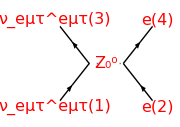
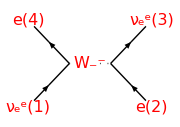
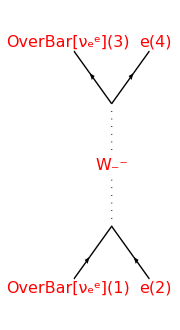
The diagrams are constrained by possible vertices: {W_-^-→{e,(ν̄)_e}}
{Z_0^0→{fermion,OverBar[fermion]}}where the fermion corresponds to one of {e,ν}. (A) The Z_0^0 exchange contributes for any neutrino {ν_e^e,ν_μ^μ,ν_τ^τ} via the diagram:
-Graphics-
(B) The W_-^- exchange contributes in the u-channel only if the neutrino is {ν_e^e}
-Graphics-
(C) The W_-^- exchange contributes in the s-channel only if the neutrino is {OverBar[ν_e^e]}
-Graphics-

```mathematica
PR1[
"The diagrams are constrained by possible vertices: ",
Column[tmp={{Wu["-"]->{e,Subscript[ν̄, e]}},{Zu[0]->{fermion,OverBar[fermion]}}}],
"where the fermion corresponds to one of ",{e,ν},
". (A) The ",Zu[0]," exchange contributes for any neutrino ", {νd[e],νd[μ],νd[τ]}," via the diagram:",
NL,Graphics2H2[νd[eμτ][1],e[2],Zu[0],νd[eμτ][3],e[4]],
NL,"(B) The ",Wu["-"]," exchange contributes in the u-channel only if the neutrino is ",{νd[e]},
NL,Graphics2H2[νd[e][1],e[2],Wu["-"],e[4],νd[e][3]],
NL,"(C) The ",Wu["-"]," exchange contributes in the s-channel only if the neutrino is ",{OverBar[νd[e]]},
NL,Graphics2X2[OverBar[νd[e]][1],e[2],Wu["-"],OverBar[νd[e]][3],e[4]]
];
```

```mathematica
PR1["The propagator for the gauge bosons ",{Zud[0,μ],Wud["-",μ]},
NL,"The boson propagator of mass M is: ",tmpp0=tmpp=I/(k^2-M^2)((kd[μ].kd[ν])/M^2-gdd[μ,ν]),
NL,"For low energies we ignore ",k.k/M^2," terms so the scattering amplitude",yield,
tmpp={tmpp}/.kd[a_].kd[b_]/M^2->0/.k^2-M^2->M^2//First]
```

The propagator for the gauge bosons {Z_(0μ)^(0μ),W_-μ^-μ}
The boson propagator of mass M is: (ⅈ ((k_μ^μ.k_ν^ν)/M^2-g_μν^μν))/(k^2-M^2)
For low energies we ignore (k.k)/M^2 terms so the scattering amplitude ⟶ -(ⅈ g_μν^μν)/M^2

```mathematica
scalars={g,Zd[_],Sec[_],Sin[_],Tan[_],Cos[_],gdd[_,_],Power[_,_]};
PR1["The Z-exchange amplitude is then ","POFF",
tmp=(tmpLZ/.u[ν]->0).(tmpp/.M->Subscript[M, Z]).(tmpLZ/.μ->ν/.u[e]->0)/.Zd[_]->1,Yield,
tmp=tmp//.simpleDot2[scalars]//Simplify,Yield,"PON",
tmp=tmp/.HoldPattern[Dot[a__]]:>Dot[a][[-4;;]]Dot[a][[;;-5]]//Simplify,Yield,
tmp=tmp//TrigExpand;
tmpaZ2=Collect[tmp,{HoldPattern[Dot[__]],gdd[_,_],Subscript[G, F],g,α},Simplify],
NL,"By comparing this with the desired form we can almost pick off the value of ",{Subscript[g, L],Subscript[g, R]}," where the terms for left- and right-handed electron respectively are ",
tmpgL=tmp/.Subscript[P, R]->0//.simpleDot,and,
tmpgR=tmp-tmpgL,Imply,
tmpgL=-4 Subscript[G, F]/(√2)Subscript[g, L]->-I(tmpgL/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgL=RuleX[tmpgL,Subscript[g, L]]//Simplify,and,(*verify -I ?from amplitude->-I M? *)
tmpgR=-4 Subscript[G, F]/(√2)Subscript[g, R]->-I(tmpgR/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgR=RuleX[tmpgR,Subscript[g, R]]//Simplify,
NL,"These relationship are for non-electron neutrinos. ",
NL,"Introducing the Fermi constant (20.95), G_F, ",
subG={Subscript[G, F]->g^2 √2/(8 Subscript[M, W]^2),Subscript[M, W]->Subscript[M, Z] Cos[θw]},Imply,
tmpgLRZ={tmpgL,tmpgR}//.subG//Flatten//Simplify
]
```

The Z-exchange amplitude is then 1/(4 M_Z^2)ⅈ g^2 OverBar[u[ν]].γ_ν^ν.P_L.u[ν] (Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] Sec[θw]^2-2 OverBar[u[e]].γ_μ^μ.P_R.u[e] Tan[θw]^2) g_μν^μν
→ (ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
By comparing this with the desired form we can almost pick off the value of {g_L,g_R} where the terms for left- and right-handed electron respectively are (ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(4 M_Z^2) and (ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(4 M_Z^2)
⇒ -2 √2 g_L G_F→-ⅈ ((ⅈ g^2)/(4 M_Z^2)-(ⅈ g^2 Tan[θw]^2)/(4 M_Z^2)) ⟶ {g_L→(g^2 (-1+Tan[θw]^2))/(8 √2 G_F M_Z^2)} and -2 √2 g_R G_F→-ⅈ ((ⅈ g^2)/(4 M_Z^2)-(ⅈ g^2 Sec[θw]^2)/(4 M_Z^2)-(ⅈ g^2 Tan[θw]^2)/(4 M_Z^2)) ⟶ {g_R→(g^2 Tan[θw]^2)/(4 √2 G_F M_Z^2)}
These relationship are for non-electron neutrinos. 
Introducing the Fermi constant (20.95), G_F, {G_F→g^2/(4 √2 M_W^2),M_W→Cos[θw] M_Z}
⇒ {g_L→-1/2 Cos[2 θw],g_R→Sin[θw]^2}

```mathematica
PR1["The ν[e]-e amplitude has contribution from the above W-exchange diagram (B).",
tmp=(tmpWu[[1]]).(tmpp/.M->Subscript[M, W]).(tmpWu[[2]]/.μ->ν)/.Wud[_,_]->1,yield,
tmpaW=tmp//.simpleDot2[scalars]//Simplify//Flatten,
NL,"The Fierz identity transforms this into Z-exchange form ",
tmpaW=tmpaW/.HoldPattern[Dot[a__,ν,b__,e]]->-Dot[a,Subscript[P, L],e]Dot[b,Subscript[P, L],ν],
NL,"This is added to the Z-exchange term: ",CR[" The opposite sign is due to anti-commutation of the eν operators(?).  How is this different from the Fierz identity?"],
tmp=tmpaZ2-tmpaW,Yield,
tmpaZW=Collect[tmp,{HoldPattern[Dot[__]],gdd[_,_],Subscript[G, F],g},Simplify],
NL,"Using the relationship: ",sub={Subscript[M, W]->Subscript[M, Z] Cos[θw]},Yield,
tmpaZW/.sub,Yield,
NL,"Again by comparing this with the desired form we can almost pick off the value of ",{Subscript[g, L],Subscript[g, R]}," where the terms for left- and right-handed electron respectively are ",
tmpgL=tmp/.Subscript[P, R]->0//.simpleDot,and,
tmpgR=tmp-tmpgL,Imply,
tmpgL=-4 Subscript[G, F]/(√2)Subscript[g, L]->-I(tmpgL/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgL=RuleX[tmpgL,Subscript[g, L]]//Simplify,and,(*verify -I*)
tmpgR=-4 Subscript[G, F]/(√2)Subscript[g, R]->-I(tmpgR/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgR=RuleX[tmpgR,Subscript[g, R]]//Simplify,
NL,"These relationship are for electron neutrinos, ν[e]. ",Imply,
tmpgLRnu={tmpgL,tmpgR}//.subG//Flatten//Simplify
]
```

The ν[e]-e amplitude has contribution from the above W-exchange diagram (B).(g OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e])/(√2).(-(ⅈ g_μν^μν)/M_W^2).(g OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-])/(√2) ⟶ -(ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] g_μν^μν)/(2 M_W^2)
The Fierz identity transforms this into Z-exchange form -(ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] g_μν^μν)/(2 M_W^2)
This is added to the Z-exchange term:  The opposite sign is due to anti-commutation of the eν operators(?).  How is this different from the Fierz identity?(ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] g_μν^μν)/(2 M_W^2)+(ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
→ (ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] g_μν^μν)/(2 M_W^2)+(ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
Using the relationship: {M_W→Cos[θw] M_Z}
→ (ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)+(ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] Sec[θw]^2 g_μν^μν)/(2 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
→ 
Again by comparing this with the desired form we can almost pick off the value of {g_L,g_R} where the terms for left- and right-handed electron respectively are (ⅈ g^2 OverBar[u[e_-^-]].γ_μ^μ.P_L.u[ν_e^e].OverBar[u[ν_e^e]].γ_ν^ν.P_L.u[e_-^-] g_μν^μν)/(2 M_W^2)+(ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2) and -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
⇒ -2 √2 g_L G_F→-ⅈ ((ⅈ g^2)/(2 M_W^2)+(ⅈ g^2 Cos[2 θw] Sec[θw]^2)/(4 M_Z^2)) ⟶ {g_L→-(g^2 (Cos[2 θw] Sec[θw]^2 M_W^2+2 M_Z^2))/(8 √2 G_F M_W^2 M_Z^2)} and -2 √2 g_R G_F→-(g^2 Tan[θw]^2)/(2 M_Z^2) ⟶ {g_R→(g^2 Tan[θw]^2)/(4 √2 G_F M_Z^2)}
These relationship are for electron neutrinos, ν[e]. 
⇒ {g_L→-1-1/2 Cos[2 θw],g_R→Sin[θw]^2}

```mathematica
PR1["(c) The amplitude for the ν̄+e interaction has additional contribution from the s-channel W-exchange diagram (C) and where the spinor representation of anti-fermions ν̄ is v[ν] where {1,2} label incoming and {3,4} label outgoing particles: ",
tmp=(tmpWu[[1]]/.{u[νd[a_]]->v[νd[a][3]],u[eu[a_]]->u[eu[a][4]]}).(tmpp/.M->Subscript[M, W]).(tmpWu[[2]]/.{u[νd[a_]]->v[νd[a][1]],u[eu[a_]]->u[eu[a][2]],γu[μ]->γu[ν]})/.Wud[_,_]->1,yield,
tmpaW=tmp//.simpleDot2[scalars]//Simplify//Flatten,
NL,"The Fierz identity transforms this into: ",
tmpaW=tmpaW/.HoldPattern[Dot[a__,v[c_],b__,u[d_]]]->-Dot[a,u[d]]Dot[b,v[c]],
CR[" We can relate anti-fermion spinors to fermionic spinors by charge conjugation, C, which gives the same value for the matrix element.  Using the table on p.71 we can write (Note that P_L->P_R): "],
tmpvv=ExtractPositionPattern[tmpaW,HoldPattern[Dot[a__,v[_]]]];
tmp=tmpvv[[1,2]],yield,
tmp=C.tmp.C,yield,
tmpvv[[1,2]]=-tmp[[2;;-2]]/.Subscript[P, L]->Subscript[P, R]/.v->u//Swap[{νd[e][1],νd[e][3]}];tmpvv,yield,
tmpaW=ReplacePart[tmpaW,tmpvv],
NL,"Return to more ambiguous notation: ",
tmpaW=tmpaW/.u[Tensor[a_,_,_][_]]->u[a],
CR["The P_R make it not compatible with the Z amplitude.  Perhaps we should use CPT invariance, then the current would change by P_R->P_L. "],
tmpaW=tmpaW/.Subscript[P, R]->Subscript[P, L],
NL,"This is added to the Z-exchange term: ",
tmpgLRZW=tmpaZ2+tmpaW
]
```

(c) The amplitude for the ν̄+e interaction has additional contribution from the s-channel W-exchange diagram (C) and where the spinor representation of anti-fermions ν̄ is v[ν] where {1,2} label incoming and {3,4} label outgoing particles: (g OverBar[u[e_-^-[4]]].γ_μ^μ.P_L.v[ν_e^e[3]])/(√2).(-(ⅈ g_μν^μν)/M_W^2).(g OverBar[v[ν_e^e[1]]].γ_ν^ν.P_L.u[e_-^-[2]])/(√2) ⟶ -(ⅈ g^2 OverBar[u[e_-^-[4]]].γ_μ^μ.P_L.v[ν_e^e[3]].OverBar[v[ν_e^e[1]]].γ_ν^ν.P_L.u[e_-^-[2]] g_μν^μν)/(2 M_W^2)
The Fierz identity transforms this into: (ⅈ g^2 OverBar[u[e_-^-[4]]].γ_μ^μ.P_L.u[e_-^-[2]] OverBar[v[ν_e^e[1]]].γ_ν^ν.P_L.v[ν_e^e[3]] g_μν^μν)/(2 M_W^2) We can relate anti-fermion spinors to fermionic spinors by charge conjugation, C, which gives the same value for the matrix element.  Using the table on p.71 we can write (Note that P_L->P_R): OverBar[v[ν_e^e[1]]].γ_ν^ν.P_L.v[ν_e^e[3]] ⟶ C.OverBar[v[ν_e^e[1]]].γ_ν^ν.P_L.v[ν_e^e[3]].C ⟶ {{4}→-OverBar[u[ν_e^e[3]]].γ_ν^ν.P_R.u[ν_e^e[1]]} ⟶ -(ⅈ g^2 OverBar[u[e_-^-[4]]].γ_μ^μ.P_L.u[e_-^-[2]] OverBar[u[ν_e^e[3]]].γ_ν^ν.P_R.u[ν_e^e[1]] g_μν^μν)/(2 M_W^2)
Return to more ambiguous notation: -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_R.u[ν] g_μν^μν)/(2 M_W^2)The P_R make it not compatible with the Z amplitude.  Perhaps we should use CPT invariance, then the current would change by P_R->P_L. -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] g_μν^μν)/(2 M_W^2)
This is added to the Z-exchange term: -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] g_μν^μν)/(2 M_W^2)+(ⅈ g^2 Cos[2 θw] OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Sec[θw]^2 g_μν^μν)/(4 M_Z^2)-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)

```mathematica
PR1[
tmp=Collect[tmpgLRZW,{HoldPattern[Dot[__]],gdd[_,_],Subscript[G, F],g},Simplify],
NL,"Using the relationship: ",sub={Subscript[M, W]->Subscript[M, Z] Cos[θw]},Yield,
tmp=tmp/.sub,Yield,
NL,"Again by comparing this with the desired form we can almost pick off the value of ",{Subscript[g, L],Subscript[g, R]}," where the terms for left- and right-handed electron respectively are ",
tmpgL=tmp/.Subscript[P, R]->0//.simpleDot,and,
tmpgR=tmp-tmpgL,Imply,tmpgL=-4 Subscript[G, F]/(√2)Subscript[g, L]->-I(tmpgL/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgL=RuleX[tmpgL,Subscript[g, L]]//Simplify,and,(*verify -I*)
tmpgR=-4 Subscript[G, F]/(√2)Subscript[g, R]->-I(tmpgR/.{HoldPattern[Dot[__]]->1,gdd[_,_]->1}),yield,
tmpgR=RuleX[tmpgR,Subscript[g, R]]//Simplify,Imply,
tmpgLRnubar={tmpgL,tmpgR}//.subG//Flatten//Simplify
]
```

-(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)-1/4 ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] (2/M_W^2+(-1+Tan[θw]^2)/M_Z^2) g_μν^μν
Using the relationship: {M_W→Cos[θw] M_Z}
→ -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)-1/4 ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] ((2 Sec[θw]^2)/M_Z^2+(-1+Tan[θw]^2)/M_Z^2) g_μν^μν
→ 
Again by comparing this with the desired form we can almost pick off the value of {g_L,g_R} where the terms for left- and right-handed electron respectively are -1/4 ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_L.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] ((2 Sec[θw]^2)/M_Z^2+(-1+Tan[θw]^2)/M_Z^2) g_μν^μν and -(ⅈ g^2 OverBar[u[e]].γ_μ^μ.P_R.u[e] OverBar[u[ν]].γ_ν^ν.P_L.u[ν] Tan[θw]^2 g_μν^μν)/(2 M_Z^2)
⇒ -2 √2 g_L G_F→-1/4 g^2 ((2 Sec[θw]^2)/M_Z^2+(-1+Tan[θw]^2)/M_Z^2) ⟶ {g_L→-(g^2 (-2+Cos[2 θw]) Sec[θw]^2)/(8 √2 G_F M_Z^2)} and -2 √2 g_R G_F→-(g^2 Tan[θw]^2)/(2 M_Z^2) ⟶ {g_R→(g^2 Tan[θw]^2)/(4 √2 G_F M_Z^2)}
⇒ {g_L→1-1/2 Cos[2 θw],g_R→Sin[θw]^2}

```mathematica
PR1["So we have ",{Subscript[g, L],Subscript[g, R]}," for the three cases: ",
{{{e,ν≠{ν[e],OverBar[ν[e]]}}->tmpgLRZ},
{{e,ν==ν[e]}->tmpgLRnu},
{{e,ν==OverBar[ν[e]]}->tmpgLRnubar}}
]
```

So we have {g_L,g_R} for the three cases: {{{e,ν≠{ν[e],OverBar[ν[e]]}}→{g_L→-1/2 Cos[2 θw],g_R→Sin[θw]^2}},{{e,ν==ν[e]}→{g_L→-1-1/2 Cos[2 θw],g_R→Sin[θw]^2}},{{e,ν==OverBar[ν[e]]}→{g_L→1-1/2 Cos[2 θw],g_R→Sin[θw]^2}}}

```mathematica
PR1["(4) A_FB--Forward-Backward Asymmetry on the Z Peak.  
Consider the process ",tmpef={eu["+"],eu["-"]}⟶{f̄,f}," at ",√s->Subscript[M, Z]," where f is any Dirac fermion of the standard model whose mass we can neglect compared with M_Z.  Let θ be the angle of f with respect to the eletron beam direction in the center of mas frame.  Define the forward-backward asymmetry for f by ",
tmpAFB=Aud[f,FB]->(σud[f,F]-σud[f,B])/(σud[f,F]+σud[f,B]),
" where ",σud[f,F(B)]," is the cross section with ",Cos[θw]," positive(negative).  Neglecting non-leading terms from photon exchange, which are down by powers of ",Subscript[Γ, Z]/Subscript[M, Z]," compute ",Aud[f,FB]," in the standard model in terms of ",{Sin[θw]^2,Qd[f],"electric charge of f",Abs[Qd[f]]},
"(There is also a polarization, or left-right asymmetry, which is very easy to calculate--see Peskin and Schroeder p.710 and (20.96))"
]
```

(4) A_FB--Forward-Backward Asymmetry on the Z Peak.  
Consider the process {e_+^+,e_-^-}⟶{f̄,f} at √s→M_Z where f is any Dirac fermion of the standard model whose mass we can neglect compared with M_Z.  Let θ be the angle of f with respect to the eletron beam direction in the center of mas frame.  Define the forward-backward asymmetry for f by A_fFB^fFB→(-σ_fB^fB+σ_fF^fF)/(σ_fB^fB+σ_fF^fF) where σ_(fB F)^(fB F) is the cross section with Cos[θw] positive(negative).  Neglecting non-leading terms from photon exchange, which are down by powers of Γ_Z/M_Z compute A_fFB^fFB in the standard model in terms of {Sin[θw]^2,Q_f^f,electric charge of f,Abs[Q_f^f]}(There is also a polarization, or left-right asymmetry, which is very easy to calculate--see Peskin and Schroeder p.710 and (20.96))

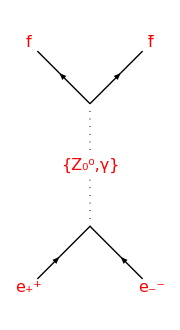
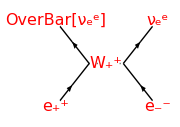
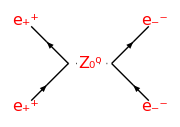
Map out the possible diagrams of {e_+^+,e_-^-}⟶{f̄,f}
(A):-Graphics-(B):-Graphics-(C):-Graphics-

```mathematica
PR1["Map out the possible diagrams of ",tmpef,
NL,"(A):",Graphics2X2[eu["+"],eu["-"],{Zu[0],γ},f,f̄],
"(B):",Graphics2H2[eu["+"],eu["-"],Wu["+"],OverBar[νd[e]],νd[e]],
"(C):",Graphics2H2[eu["+"],eu["-"],Zu[0],eu["+"],eu["-"]]
]
```

```mathematica
PR1["Examine the propagator term as k^2⟶ M_Z^2: ",tmpp0,
NL,"Diagram (B) has a neglible contribution because values in the propagator: ",
subM={M->Subscript[M, W],k^2->Subscript[M, Z]^2},yield,
tmp=tmpp0/.subM,yield,
tmp=tmp/.subg//Simplify,
NL,"which is small compared with the other propagators at resonance if Csc[θw] has a moderate value.",
NL,"The Breit-Wigner propagator for (A): ",subM={k^2->Subscript[M, Z]^2,M->Subscript[M, Z],Γ->Subscript[Γ, Z]},yield,tmpbw=-I gdd[μ,ν]/(k^2-M^2+I M Γ),yield,
tmpbw=tmpbw/.subM,
NL,"The same propagator for diagram (C)."
]
```

Examine the propagator term as k^2⟶ M_Z^2: (ⅈ ((k_μ^μ.k_ν^ν)/M^2-g_μν^μν))/(k^2-M^2)
Diagram (B) has a neglible contribution because values in the propagator: {M→M_W,k^2→M_Z^2} ⟶ (ⅈ ((k_μ^μ.k_ν^ν)/M_W^2-g_μν^μν))/(-M_W^2+M_Z^2) ⟶ (ⅈ Csc[θw]^2 (k_μ^μ.k_ν^ν Sec[θw]^2-M_Z^2 g_μν^μν))/M_Z^4
which is small compared with the other propagators at resonance if Csc[θw] has a moderate value.
The Breit-Wigner propagator for (A): {k^2→M_Z^2,M→M_Z,Γ→Γ_Z} ⟶ -(ⅈ g_μν^μν)/(k^2-M^2+ⅈ M Γ) ⟶ -g_μν^μν/(M_Z Γ_Z)
The same propagator for diagram (C).

```mathematica
scalars={g,Zd[_],Sec[_],Sin[_],Tan[_],Cos[_],gdd[_,_],Power[_,_],Subscript[Γ, _]};
DefineTensorShortcuts[{{f},1}];
```

```mathematica
PR1["The f+f̄ vertex can be determined from the interaction Lagrangian as in part(a): ",
tmpLZ0,
NL,"Substitute ",subcf=c[f]->ExtractPattern[tmpLZ0, a__ Zd[μ]][[1]],yield,
tmp=tmpLZ0/.Reverse[subcf],
NL,"For the incoming electrons: ",
sub={ψ̄->OverBar[v[e2]],ψ->u[e1],c[f]->c[e1]},yield,
tmpLZfa=tmp/.sub,
NL,"For the outgoing fermions: ",
sub={ψ̄->OverBar[u[f3]],ψ->v[f4],c[f]->c[f4]},yield,
tmpLZfb=tmp/.sub,
NL,"where a L-R projection operator P[LR] is included in the definition of c[f]."
]
```

The f+f̄ vertex can be determined from the interaction Lagrangian as in part(a): ⅈ ψ̄.γ_μ^μ.(-ⅈ g Sec[θw] (-Q Sin[θw]^2+T_3^3) Z_μ^μ).ψ
Substitute c[f]→-ⅈ g Sec[θw] (-Q Sin[θw]^2+T_3^3) Z_μ^μ ⟶ ⅈ ψ̄.γ_μ^μ.c[f].ψ
For the incoming electrons: {ψ̄→OverBar[v[e2]],ψ→u[e1],c[f]→c[e1]} ⟶ ⅈ OverBar[v[e2]].γ_μ^μ.c[e1].u[e1]
For the outgoing fermions: {ψ̄→OverBar[u[f3]],ψ→v[f4],c[f]→c[f4]} ⟶ ⅈ OverBar[u[f3]].γ_μ^μ.c[f4].v[f4]
where a L-R projection operator P[LR] is included in the definition of c[f].

```mathematica
PR1["Compose the amplitude: ",
tmp=tmpMee=I ℳ->tmpLZfa.tmpbw.(tmpLZfb/.μ->ν),Yield,
tmp=tmp//.simpleDot2[{gdd[_,_],Power[_,_]}];
tmpM1=tmp/.HoldPattern[Dot[a__,u[b_],OverBar[u[c_]],d__]]->Dot[a,u[b]]Dot[OverBar[u[c]],d],
NL,"In computing the cross-section: ",
tmpσ=σ∝Abs[tmp[[1]]]^2,
" first determine ConjugateTranspose[ℳ]: ",
tmp=SuperDagger[tmpM1[[2]]]/.subDaggerCT//ConjugateCTSimplify1[{Power[_,_],Subscript[M, _],Subscript[Γ, _],gdd[_,_],g},{Power[_,_],gdd[_,_],P[LR],g,Tu[_],Q,c[_]}],Yield,
tmp=tmp/.OverBar[a_]->SuperDagger[a].γu[0]/.subDaggerCT//.simpleGamma,
NL,"using the definition of cL and cR as: ",subc=c[a_]->cL[a] Subscript[P, L]+cR[a] Subscript[P, R],Yield,
tmp=tmp/.subc,Yield,
tmp=tmp//ConjugateCTSimplify1[{Subscript[P, _]}]//DotExpandAll,Yield,
scalars={cL[_],cR[_],SuperStar[cR[_]],SuperStar[cL[_]]}/.subDaggerCT;
tmp=tmp//.simpleDot2[scalars],Yield,
tmp=tmp/.Dot->xDot/.xDot[a_,Subscript[P, b_],γu[c_],γu[d_],e_]->xDot[a,γu[c],γu[d],Subscript[P, b],e],Yield,
tmpMc=tmp/.xDot[ConjugateTranspose[a_],γu[0],b__]->Dot[ā,b]//.{μ->μc,ν->νc}
]
```

Compose the amplitude: ⅈ ℳ→(ⅈ OverBar[v[e2]].γ_μ^μ.c[e1].u[e1]).(-g_μν^μν/(M_Z Γ_Z)).(ⅈ OverBar[u[f3]].γ_ν^ν.c[f4].v[f4])
→ ⅈ ℳ→(OverBar[u[f3]].γ_ν^ν.c[f4].v[f4] OverBar[v[e2]].γ_μ^μ.c[e1].u[e1] g_μν^μν)/(M_Z Γ_Z)
In computing the cross-section: σ∝Abs[ℳ]^2 first determine ConjugateTranspose[ℳ]: (u[e1]^†.c[e1]^*.(γ_μ^μ)^†.OverBar[v[e2]]^† v[f4]^†.c[f4]^*.(γ_ν^ν)^†.OverBar[u[f3]]^† g_μν^μν)/(M_Z Γ_Z)
→ (u[e1]^†.c[e1]^*.γ_0^0.γ_μ^μ.v[e2] v[f4]^†.c[f4]^*.γ_0^0.γ_ν^ν.u[f3] g_μν^μν)/(M_Z Γ_Z)
using the definition of cL and cR as: c[a_]→cL[a] P_L+cR[a] P_R
→ 1/(M_Z Γ_Z)u[e1]^†.(cL[e1] P_L+cR[e1] P_R)^*.γ_0^0.γ_μ^μ.v[e2] v[f4]^†.(cL[f4] P_L+cR[f4] P_R)^*.γ_0^0.γ_ν^ν.u[f3] g_μν^μν
→ 1/(M_Z Γ_Z)(u[e1]^†.(cL[e1]^* P_L).γ_0^0.γ_μ^μ.v[e2]+u[e1]^†.(cR[e1]^* P_R).γ_0^0.γ_μ^μ.v[e2]) (v[f4]^†.(cL[f4]^* P_L).γ_0^0.γ_ν^ν.u[f3]+v[f4]^†.(cR[f4]^* P_R).γ_0^0.γ_ν^ν.u[f3]) g_μν^μν
→ 1/(M_Z Γ_Z)(cL[e1]^* u[e1]^†.P_L.γ_0^0.γ_μ^μ.v[e2]+cR[e1]^* u[e1]^†.P_R.γ_0^0.γ_μ^μ.v[e2]) (cL[f4]^* v[f4]^†.P_L.γ_0^0.γ_ν^ν.u[f3]+cR[f4]^* v[f4]^†.P_R.γ_0^0.γ_ν^ν.u[f3]) g_μν^μν
→ 1/(M_Z Γ_Z)g_μν^μν (cL[e1]^* xDot[u[e1]^†,γ_0^0,γ_μ^μ,P_L,v[e2]]+cR[e1]^* xDot[u[e1]^†,γ_0^0,γ_μ^μ,P_R,v[e2]]) (cL[f4]^* xDot[v[f4]^†,γ_0^0,γ_ν^ν,P_L,u[f3]]+cR[f4]^* xDot[v[f4]^†,γ_0^0,γ_ν^ν,P_R,u[f3]])
→ 1/(M_Z Γ_Z)(cL[e1]^* OverBar[u[e1]].γ_μc^μc.P_L.v[e2]+cR[e1]^* OverBar[u[e1]].γ_μc^μc.P_R.v[e2]) (cL[f4]^* OverBar[v[f4]].γ_νc^νc.P_L.u[f3]+cR[f4]^* OverBar[v[f4]].γ_νc^νc.P_R.u[f3]) g_μcνc^μcνc

```mathematica
PR1["Substituting for c[] for M: ",Yield,
tmp=tmpM1,Yield,
tmp=tmp/.subc,Yield,
tmp=tmp//ConjugateCTSimplify1[{Subscript[P, _]}]//DotExpandAll,Yield,
scalars={cL[_],cR[_],SuperStar[cR[_]],SuperStar[cL[_]]}/.subDaggerCT;
tmpM2=tmp//.simpleDot2[scalars]
]
```

Substituting for c[] for M: 
→ ⅈ ℳ→(OverBar[u[f3]].γ_ν^ν.c[f4].v[f4] OverBar[v[e2]].γ_μ^μ.c[e1].u[e1] g_μν^μν)/(M_Z Γ_Z)
→ ⅈ ℳ→(OverBar[u[f3]].γ_ν^ν.(cL[f4] P_L+cR[f4] P_R).v[f4] OverBar[v[e2]].γ_μ^μ.(cL[e1] P_L+cR[e1] P_R).u[e1] g_μν^μν)/(M_Z Γ_Z)
→ ⅈ ℳ→1/(M_Z Γ_Z)(OverBar[u[f3]].γ_ν^ν.(cL[f4] P_L).v[f4]+OverBar[u[f3]].γ_ν^ν.(cR[f4] P_R).v[f4]) (OverBar[v[e2]].γ_μ^μ.(cL[e1] P_L).u[e1]+OverBar[v[e2]].γ_μ^μ.(cR[e1] P_R).u[e1]) g_μν^μν
→ ⅈ ℳ→1/(M_Z Γ_Z)(cL[f4] OverBar[u[f3]].γ_ν^ν.P_L.v[f4]+cR[f4] OverBar[u[f3]].γ_ν^ν.P_R.v[f4]) (cL[e1] OverBar[v[e2]].γ_μ^μ.P_L.u[e1]+cR[e1] OverBar[v[e2]].γ_μ^μ.P_R.u[e1]) g_μν^μν

```mathematica
PR1["So ",tmpσ1=tmpσ->SuperDagger[tmpM1[[1]]].tmpM1[[1]]->(tmpMc)tmpM2[[2]],Yield,
tmp=tmpσ1[[2,2]]/.subc//.simpleDot2[{Power[_,_],gdd[_,_]}],
NL,"Summing over polarizations (see manipulation around (5.3).) ","POFF",
tmp=Expand[tmp]/.Dot->xDot//.xDot[a__,v[b_]]d__ xDot[OverBar[v[b_]],c__]->xDot[a,Slash[p][b]-m[b],c]d /.xDot[OverBar[u[b_]],a__,u[b_]]->Tr[xDot[Slash[p][b]+m[p],a]]/.xDot->Dot,"PON",
NL,"Neglect m[] masses ",Yield,
tmpσ2=tmp/.m[_]->0
]
```

So σ∝Abs[ℳ]^2→(ⅈ ℳ)^†.(ⅈ ℳ)→1/(M_Z^2 Γ_Z^2)(cL[e1]^* OverBar[u[e1]].γ_μc^μc.P_L.v[e2]+cR[e1]^* OverBar[u[e1]].γ_μc^μc.P_R.v[e2]) (cL[f4] OverBar[u[f3]].γ_ν^ν.P_L.v[f4]+cR[f4] OverBar[u[f3]].γ_ν^ν.P_R.v[f4]) (cL[e1] OverBar[v[e2]].γ_μ^μ.P_L.u[e1]+cR[e1] OverBar[v[e2]].γ_μ^μ.P_R.u[e1]) (cL[f4]^* OverBar[v[f4]].γ_νc^νc.P_L.u[f3]+cR[f4]^* OverBar[v[f4]].γ_νc^νc.P_R.u[f3]) g_μν^μν g_μcνc^μcνc
→ 1/(M_Z^2 Γ_Z^2)(cL[e1]^* OverBar[u[e1]].γ_μc^μc.P_L.v[e2]+cR[e1]^* OverBar[u[e1]].γ_μc^μc.P_R.v[e2]) (cL[f4] OverBar[u[f3]].γ_ν^ν.P_L.v[f4]+cR[f4] OverBar[u[f3]].γ_ν^ν.P_R.v[f4]) (cL[e1] OverBar[v[e2]].γ_μ^μ.P_L.u[e1]+cR[e1] OverBar[v[e2]].γ_μ^μ.P_R.u[e1]) (cL[f4]^* OverBar[v[f4]].γ_νc^νc.P_L.u[f3]+cR[f4]^* OverBar[v[f4]].γ_νc^νc.P_R.u[f3]) g_μν^μν g_μcνc^μcνc
Summing over polarizations (see manipulation around (5.3).) 
Neglect m[] masses 
→ 1/(M_Z^2 Γ_Z^2)cL[e1] cL[f4] cL[e1]^* cL[f4]^* g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[f4] cL[e1]^* cL[f4]^* cR[e1] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[f4] cL[f4]^* cR[e1]^* g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[f4] cL[f4]^* cR[e1]^* cR[e1] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[f4] cL[e1]^* cR[f4]^* g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[f4] cL[e1]^* cR[f4]^* cR[e1] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[f4] cR[e1]^* cR[f4]^* g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[f4] cR[e1]^* cR[f4]^* cR[e1] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_L.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[e1]^* cL[f4]^* cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[e1]^* cL[f4]^* cR[e1] cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[f4]^* cR[e1]^* cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[f4]^* cR[e1]^* cR[e1] cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_L]+1/(M_Z^2 Γ_Z^2)cL[e1] cL[e1]^* cR[f4]^* cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[e1]^* cR[f4]^* cR[e1] cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_L.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cL[e1] cR[e1]^* cR[f4]^* cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_L] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_R]+1/(M_Z^2 Γ_Z^2)cR[e1]^* cR[f4]^* cR[e1] cR[f4] g_μν^μν g_μcνc^μcνc Tr[(p/)[e1].γ_μc^μc.P_R.(p/)[e2].γ_μ^μ.P_R] Tr[(p/)[f3].γ_ν^ν.P_R.(p/)[f4].γ_νc^νc.P_R]

```mathematica
PR1["Continue to simplify: ",Yield,"POFF",
tmp=tmpσ2//ConjugateCTSimplify1[{Subscript[P, _]}]//DotExpandAll,Yield,
scalars={cL[_],cR[_],SuperStar[cR[_]],SuperStar[cL[_]]}/.subDaggerCT;
tmp=tmp//.simpleDot2[scalars],Yield,
tmp=tmp//.simpleTr2[scalars],
NL,"Anti-commutation of γ's means that {P_L,P_R} switch as they cross γ's.",yield,
tmp=tmp//.Tr[Dot[a__]]:>Tr[MovePairRight[{Subscript[P, L],Subscript[P, R]}][Dot[a]]],
NL,"Using definitions of P_LP_R->0, P_LP_L->P_L  ",Yield,
tmp=tmpσ3//.Tr[Dot[a___,Subscript[P, c_],Subscript[P, c_],b___]]:>Tr[Dot[a,Subscript[P, c],b]]//.Tr[Dot[a___,Subscript[P, c_],Subscript[P, d_],b___]]:>Tr[Dot[a,0,b]]/.simpleDot/.simpleTr,"PON",
NL,"This is (45): ",NL,
tmpσ3=tmp//MetricContractGexp[g]//Simplify
]
```

Continue to simplify: 
→ 
This is (45): 
tmpσ3

```mathematica
PR1["Add P_L,P_R definitions: ",sub={Subscript[P, R]->(1+γu[5])/2,Subscript[P, L]->(1-γu[5])/2},Yield,
tmp=tmpσ3/.Slash[p][a_]->pd[a]γu[a]/.sub,Yield,
tmp=tmp//.simpleTr2[{pd[_]}],Yield,
tmpσ4=tmp//MetricContractGexp[g]
]
```

Add P_L,P_R definitions: {P_R→1/2 (1+γ_5^5),P_L→1/2 (1-γ_5^5)}
→ tmpσ3
→ tmpσ3
→ tmpσ3

```mathematica
PR1[TCOLOR[Red],"Add p indices for index manipulation:",Yield,"POFF",
tmp=tmpσ4/.pd[a_]->pd[a][a],Yield,
tmp=tmp/.subTraceGamma0//Expand//MetricContractGexp[g],Yield,
tmp=tmp/.simpleGamma//.simpleTr2[{}],Yield,
tmp=tmp//simpleϵ//SwapUpDownIndices[{νc,ν,μc,μ}],Yield,(*So next step works*)
tmp=tmp/.subTraceGamma0//Expand,Yield,
tmp=tmp//MetricContractGexp[g],Yield,
(*notate dot product term so we can work on indices*)
tmp=tmp//.pu[a_][b_]pd[a_][d_]:>Sort[pu[b].pu[d]]//simpleϵ,Yield,
tmp=tmp/.Tensor[ϵ,a_,b_]:>Orderϵ[Tensor[ϵ,a,b]]/. ϵuuud[a_,b_,c_,d_] pu[d_][e_]->ϵuuuu[a,b,c,d] pd[d][e],Yield,
tmp=tmp//simple2ϵ;
tmp=tmp/.Tensor[δ,a_,b_]->Tensor[g,a,b]//MetricContractGexp[g]//Relabelϵ;
tmp=tmp//.pu[a_][b_]pd[a_][d_]:>Sort[pu[b].pu[d]]//Expand;
tmp=tmp/.ϵuuuu[a_,b_,c_,d_]pd[c_][f4]pd[d_][f3]->-ϵuuuu[a,b,c,d]pd[c][f3]pd[d][f4];"PON",
tmpσ5=Collect[tmp,ϵuuuu[_,_,_,_]]//.{cL[a_]Conjugate[cL[a_]]->cL[a]cL[a],cR[a_]Conjugate[cR[a_]]->cR[a]cR[a]}
]
```

Add p indices for index manipulation:
→ tmpσ3

```mathematica
"Alternative calculation"
tmp=tmpσ3//.{cL[a_]Conjugate[cL[a_]]->cL[a]cL[a],cR[a_]Conjugate[cR[a_]]->cR[a]cR[a]};
sub={Subscript[P, R]->(1+γu[5])/2,Subscript[P, L]->(1-γu[5])/2};
tmp=tmp/.sub;
tmp=ExpandAll[tmp]//.DotExpand//.simpleTr2[{}]//Simplify;
scalars={pu[_][_]};
tmp=tmp/.Slash[p][a_]->pu[a][a]γd[a]//.simpleTr2[scalars];
tmp=tmp/.subTraceGamma0//Expand;
tmp=tmp//MetricContractG;
tmp=tmp//simpleϵ;
tmp=tmp//.Tensor[ϵ,a_,b_]:>Orderϵ[Tensor[ϵ,a,b]];
tmp=tmp//simple2ϵ//Expand;
tmp=tmp/.Tensor[δ,a_,b_]->Tensor[g,a,b]//MetricContractG;
tmp=tmp//Relabelϵ//SwapUpDownIndices[{ϵ[3],ϵ[4]}];
tmp=tmp//.pu[a_][b_]pd[a_][d_]:>Sort[pu[b].pu[d]]
```

Alternative calculation

tmpσ3

```mathematica
PR1["Substitute kinematics: e-e CM at Energy is M_Z of experiment where the angle θ is the angle between the incoming electron e1 and the outgoing fermion f3 , Assume masses of {e,f} negligible->0: ",
subE={En[i_]->Subscript[M, Z]/2,p[i_]->Subscript[M, Z]/2},Yield,
Column[
kinematics={
pu[e1].pu[e2]->En[1]En[2]+p[1] p[2],
pu[f3].pu[f4]->pu[e1].pu[e2],
pu[e2].pu[f3]->En[2] En[3]+p[2] p[3] Cos[θ],
pu[e2].pu[f4]->En[2] En[4]-p[2] p[4] Cos[θ],
pu[e1].pu[f4]->En[1] En[4]+p[1] p[4] Cos[θ],
pu[e1].pu[f3]->En[1] En[3]-p[1] p[3] Cos[θ]
}],Yield,
Column[
subk=kinematics/.subE],
NL,"So the amplitude squared becomes: ",
tmpσ[[2]]->(tmpσ6=Collect[tmpσ5//.subk //Expand,Cos[θ]])
]
```

Substitute kinematics: e-e CM at Energy is M_Z of experiment where the angle θ is the angle between the incoming electron e1 and the outgoing fermion f3 , Assume masses of {e,f} negligible->0: {En[i_]→M_Z/2,p[i_]→M_Z/2}
→ p_e1^e1.p_e2^e2→En[1] En[2]+p[1] p[2]
p_f3^f3.p_f4^f4→p_e1^e1.p_e2^e2
p_e2^e2.p_f3^f3→En[2] En[3]+Cos[θ] p[2] p[3]
p_e2^e2.p_f4^f4→En[2] En[4]-Cos[θ] p[2] p[4]
p_e1^e1.p_f4^f4→En[1] En[4]+Cos[θ] p[1] p[4]
p_e1^e1.p_f3^f3→En[1] En[3]-Cos[θ] p[1] p[3]
→ p_e1^e1.p_e2^e2→M_Z^2/2
p_f3^f3.p_f4^f4→p_e1^e1.p_e2^e2
p_e2^e2.p_f3^f3→M_Z^2/4+1/4 Cos[θ] M_Z^2
p_e2^e2.p_f4^f4→M_Z^2/4-1/4 Cos[θ] M_Z^2
p_e1^e1.p_f4^f4→M_Z^2/4+1/4 Cos[θ] M_Z^2
p_e1^e1.p_f3^f3→M_Z^2/4-1/4 Cos[θ] M_Z^2
So the amplitude squared becomes: Abs[ℳ]^2→tmpσ3

```mathematica
PR1["Integrating this for the forward and backward angles and computing the forward-backward asymmetry, A_FB: ",tmp=tmpσ6;
Column[sub={Subscript[σ, F]->Integrate[tmp Sin[θ],{θ,0,Pi/2}],
Subscript[σ, B]->Integrate[tmp Sin[θ],{θ,Pi/2,Pi}]
}],Yield,
tmp=Subscript[A, FB]->(Subscript[σ, F]-Subscript[σ, B])/(Subscript[σ, F]+Subscript[σ, B]),yield,
tmp=(tmp/.sub//Simplify)
];
```

Integrating this for the forward and backward angles and computing the forward-backward asymmetry, A_FB: σ_F→tmpσ3
σ_B→tmpσ3
→ A_FB→(-σ_B+σ_F)/(σ_B+σ_F) ⟶ A_FB→0